## Introduction of run samept

Function description:
1. This program read  “config1.txt”, “plotdata_config.txt”, and read data in /CorrDataDir/CorrDataFile to plot  samept figures
2. (x, Q) are points of  samept method (please read the tutorial note of this program)
3. plot figures for selected experiments , flavours, and observables
(observable: correlation, sensitivity (dR*correlation) of PDF and residual of data, residual central value, residual uncertainty, (expt error)/(expt central) )
figures: 2D-xQ & histograms of observable values
2D-xQ: Draw (x, Q) of an observable data on x-Q plane. colors and sizes of points are determined by the value of the observable at that point)
  
∗ #PDF set, # Figures to plot, # Experiments to include, #Functions to use in correlations, #User function parameters are for setup of the input data

∗ #x-Q figure parameters, #Histogram figure parameters, #in plots, #highlight mode, #data point size are for setup of how figures look like 

∗ datalis file, Correlation Path, Correlation File  in “plotdata_config.txt” are setup of filenames that are read in this executable. If the executable need to load PDF data f(x, Q), filenames are determined by F(x,Q) Samept Path, F(x,Q) Samept File. 
If Correlation File, F(x,Q) Samept File = “default”, data filenames are determined by #PDF set.

– output: 2D-xQ, histograms

formats of data files in ../quick_data/ are List of dimension:
“fxQ”: [[iexpt, iflavour]]
“residualNset”: [[iexpt]]
“dtacentral”: [[iexpt]]

formats of data (variables) for generating figures are List of dimension: 
“corr”: [[iexpt, iflavour]]
“dRcorr”: [[iexpt, iflavour]]
“ dR”: [[iexpt]]
“residual”: [[iexpt]]
“expterror”: [[iexpt]]

## How to Run

1. setup arguments in “config1.txt” & “plotdata_config.txt” 
2. 
a. if this file’s extension is .nb, run “control runfunc you want to run” title at bottom of your code
b. if this file’s extension is .m (script version), type math -script “filename of this file” in the terminal

## Set Working path and call .m packages

```mathematica
(*this switch is for controling of .nb& .m versions, the option of the switch depends this file is saved as .nb/.m (package) extension  *)
(*.m file could be implemented in the terminal*)
(*option: "nb" or "m"*)
ThisFileExtension="nb";
```

```mathematica
(*this switch is for controling of two versions of the executables, v1:False, v2: True
v1: read Expt IDs from config1.txt and plot all data in one x-μ figure
v2: read Expt IDs from config1.txt and plot experiments seperately, storing each Expt plots into the directory with it's name == Expt ID  
*)
LoopExptBool=False;
```

```mathematica
Switch[
ThisFileExtension,
"nb",
SetDirectory[NotebookDirectory[](*DirectoryName[$InputFileName]*) ],
"m",
SetDirectory[(*NotebookDirectory[]*)DirectoryName[$InputFileName] ],
_,
Print["file extension should be \"nb\" or \"m\""];Abort[]
];

(*20171114: 
SetDirectory[NotebookDirectory[](*DirectoryName[$InputFileName]*) ]
*)
Get["corr_proj_funcs.m"]
```

present directory: /home/botingw/Downloads/Sean_20171114/xqplotter-2447ceacd1447536c690310f5ca37f4e39baa187/bin

loading ../lib/pdfParsePDS2013.m

loading ../lib/dtareadbotingw2016.m

## Global variables

```mathematica
(*this project includes three branches: Mathematica script, python script, and webpage*)
(*
1. Mathematica script: by setting config files, users can read CTEQ analyzed data (.dta & .pds files) to extract observables by (x,μ), then generate figures by run_v4.nb. outputs are in a subdirectory of ./plots 
Advandage are that 1. users can generate many figures of many flavours, observables. 2. users can customize user define functions
 
2. python script: users can use python script to run a GUI, them set the expected outputs in the GUI. After submit, outputs will show by html format
Advantages are 1. easy to use  2. users can customize user define functions
3. webpage: users can use the python GUI on a website. outputs are in another webpage.
Advantages: 1. easy to use 2. users don't need to install Mathematica

*)
(*
modes:
1. Mathematica script
2. python script
3. webpage
*)
BranchMode=2;
```

## read correlation (and other data of FigureType in config1.txt) from the data in files

```mathematica
Quicksaveplot[]:=
Module[{(*runfunc,figureDir,myPDFsetDir,PDFsetmethod,PDFname,PDFDataDir,datalistFile,expttype,exptid*)
Jobid,PDFname,FigureType,FigureFlag,ExptidType,ExptidFlag,CorrelationArgType,CorrelationArgFlag,UserArgName,UserArgValue,
XQfigureXrange,XQfigureYrange,Hist1figureNbin,Hist1figureXrange,Hist1figureYrange,
ColorSeperator,
Size,HighlightType,HighlightMode,HighlightMode1,HighlightMode2,
UserArgFunction(*20171116*)
},
Print["begin function"];
(*set input arguments *)

(*set method of (x,Q) points, options: "samept", "grid", "sameptgrid"*)
(*sameptgrid is figures of comparison of samept data and grid data*)
PDFxQSelectMethod="samept";
Print["method to search (x,Q) points that dominate the process: ",PDFxQSelectMethod];
(*set input arguments *)


(*set config file path*)
configDir=Directory[]<>"/";(*NotebookDirectory[];*)(*DirectoryName[$InputFileName];*)
configfilename="config1.txt";

(*20170301: new config file
{runfunc,figureDir,dummy1,dummy2,PDFname,dummy3,datalistFile,expttype,exptid}=
readcorrconfigfile[configDir,configfilename];
*)
(*new config file*)
(*20171109 use readcorrconfigfile5 for new highlight range convention*)
{Jobid,PDFname,FigureType,FigureFlag,ExptidType,ExptidFlag,CorrelationArgType,CorrelationArgFlag,(*UserArgName,UserArgValue,*)
XQfigureXrange,XQfigureYrange,Hist1figureNbin,Hist1figureXrange,(*Hist1figureYrange*)dummy12,
ColorSeperator,
Size,HighlightType,HighlightMode,HighlightMode1,HighlightMode2}=
(*readcorrconfigfile4*)readcorrconfigfile5[configDir,configfilename];
Print["input arguments: ",(*readcorrconfigfile4*)readcorrconfigfile5[configDir,configfilename] ];

(*check format of arguments*)
(*xyrange*)
If[XQfigureXrange[[1]]=="auto",XQfigureXrange[[1]]=10^-6];
If[XQfigureXrange[[2]]=="auto",XQfigureXrange[[2]]=1];
If[XQfigureYrange[[1]]=="auto",XQfigureYrange[[1]]=1.3];
If[XQfigureYrange[[2]]=="auto",XQfigureYrange[[2]]=1200];

(*If[Hist1figureNbin=="auto",Hist1figureNbin=5];*)
(*
If[Hist1figureXrange[[1]]=="auto",Hist1figureXrange[[1]]=10^-6];
If[Hist1figureXrange[[2]]=="auto",Hist1figureXrange[[2]]=1];
If[Hist1figureYrange[[1]]=="auto",Hist1figureYrange[[1]]=1.3];
If[Hist1figureYrange[[2]]=="auto",Hist1figureYrange[[2]]=1200];
*)

(*bar seperator input has only 3 elements*)
If[Length[ColorSeperator]≠3,Print["color seperator percentage should be three numbers"];Abort[]];
(*should be small to large, ex: 30, 50, 70*)
If[Sort[ColorSeperator]≠ColorSeperator,Print["color seperator percentage should from small to large"];Abort[]];
(*should in 0% to 100%, ex: 35,55,77.5; 35,76,140.5 is illegal*)

(*size: if highlight mode, set size as small, can't set here, need to set when reading highlight mode of a figure type*)

(*for PDFname, test whether it is in quickdata*)
(*
If[
PDFname=="CT14NNLO",
(*printprocessbyPDFsetquicksavemode[Table[quickdatacorr[[iexpt,1]][["exptinfo","exptid"]],{iexpt,1,Length[quickdatacorr]}],datalistFile]*)"dummy",
(*Print["error, the PDFset is not CT14NNLO"];Exit[];*)"dummy"(*20170426: begin to input other PDFsets*)
];
*)

(*data information (files, directory, etc) of figures that will be plotted*)
(*read plotdata_config.txt to get arguments of plot data setting*)
plotdataconfigfilename="plotdata_config.txt";
{datalistFile,(*FxQGridDir*)dummy1,(*FxQGridFile*)dummy2,(*FxQSameptDir*)dummy3,(*FxQSameptFile*)dummy4,CorrDataDir,CorrDataFile,(*GridNx*)dummy5,(*GridNQ*)dummy6}=
readplotdataconfigfile[configDir,plotdataconfigfilename];
Print["input arguments for read plot data: ",readplotdataconfigfile[configDir,plotdataconfigfilename] ];
(*if path setting is default, set it as in quick_data directory*)
quickdataDir="../quick_data/";
If[datalistFile=="default",datalistFile="./dat16lisformathematica"];
(*
If[FxQGridDir=="default",FxQGridDir=quickdataDir];
If[FxQGridFile=="default",FxQGridFile="fxQ_grid_"<>PDFname<>"_x"<>ToString[GridNx]<>"_Q"<>ToString[GridNQ]<>".dat"];

If[FxQSameptDir=="default",FxQSameptDir=quickdataDir];
If[FxQSameptFile=="default",FxQSameptFile="fxQ_samept_"<>PDFname<>".dat"];
*)
If[CorrDataDir=="default",CorrDataDir=quickdataDir];
If[CorrDataFile=="default",
If[PDFxQSelectMethod=="samept",CorrDataFile="samept_data_"<>PDFname<>".dat"];
If[PDFxQSelectMethod=="grid",CorrDataFile="grid_data_"<>PDFname<>"_x"<>ToString[GridNx]<>"_Q"<>ToString[GridNQ]<>".dat"];
If[PDFxQSelectMethod=="xgrid",CorrDataFile="xgrid_data_"<>PDFname<>"_x"<>ToString[GridNx]<>".dat"];

If[PDFxQSelectMethod=="sameptgrid",
CorrDataFileSamept="samept_data_"<>PDFname<>".dat";CorrDataFileGrid="xgrid_data_"<>PDFname<>"_x"<>ToString[GridNx]<>".dat"];
"dummy"
];

(*for arguments which we don't want not show on web version, we setup them is web version mathematica as internal variable*)
(*
datalistFile="./dat16lisformathematica";
expttype="multi";
*)
exptid;(*it will equal to exptlist*)
figureDir="../plots/";

(*read data from data package*)
(*decide which data file to read bassed on PDFname*)
(*
quickdataDir="../quick_data/";
CorrDataDir=quickdataDir;
*)
(*correlationdatapackage=quickdataDir<>PDFname<>"_correlation_data.dat";*)
(*Nx=80;NQ=25;*)
(*20171101
Print["file status: ",FileExistsQ[CorrDataDir<>"corr_samept_data_"<>PDFname<>".dat"] ];
*)
Print["present directory:\n",Directory[]];
Print["quick correlation data:\n",FileNames[CorrDataDir<>"*samept_data_"<>PDFname<>"*"] ];
(*
If[
FileExistsQ[correlationdatapackage]==True,
(*<<correlationdatapackage*)Get[correlationdatapackage];Print["loading quick correlation data..."],
Print["error, the correlation data of PDFname ",PDFname,"does not exist in quick database"];Abort[]
];
*)


(*20170226: for quick save mode, correlation data are loaded from a .m package, so reading experimental id from .dta files are replaced by reading package*)
(*myPDFsetdtafile=FileNames[myPDFsetDir<>"*dta"][[1]];*)


(*set dta Dir you want to read data, it's the PDFset Dir you choose*)
(*20170226: don't need to load dta file for expt information and data*)
(*DtaDir=myPDFsetDir;*)
(*experiments you choose*)
(*
processes={PDISNC,NDISCC,PDISNCCC,PVBPZ,PVBPW,PJP,hDISNC,hDISCC,hVBPZ};
exptlistAll=processes//Flatten;
exptlistProtonNeutron={PDISNC,NDISCC,PDISNCCC,PVBPZ,PVBPW,PJP}//Flatten;
*)

(*20170301: exptid read by new config*)
(*exptlist=exptlistAll;*)
Print["read experimental id"];
exptlist={};
(*check argument inputs are correct*)
Nexpt1=Length[ExptidType];
Nexpt2=Length[ExptidFlag];
If[Nexpt1!=Nexpt2,Print["configure file error, # of exptid is different with # of exptidflag"];Abort[] ];

Table[
If[ExptidFlag[[iexpt]]≠0 &&ExptidFlag[[iexpt]]≠1,Print["configure file error, exptidflag is not 1 or 0"];Abort[] ]
,{iexpt,1,Length[ExptidType]}
];
(*it flag is on, add that exptid into exptlist*)(*20170410: exptlist doesn't mean the expts of final made figure because quick_data does not must have all expts*)
Table[
If[ExptidFlag[[iexpt]]==1,exptlist=Append[exptlist,ExptidType[[iexpt]] ] ],
{iexpt,1,Length[ExptidType]}
];
(*if version 2 (LoopExptBool==True;), select only n-th expt in the loop*)
If[LoopExptBool==True,exptlist={exptlist[[irun]]}];
(*20170301: exptid = exptlist*)
exptid = exptlist;




(*******************RUN*************************)
(*read experiments info (expt names)*)
(*lisTable=*)ReadLisFile[datalistFile];
(*correlation, dr*correlation, deltaR calculation *)

(*
(*calculate correlation*)
corrfxQdtaobsclass=quickdatacorr;
(*get some data from package*)
residualclass="unset";
theoryerrorclass="unset";
expterrorclass"unset";
If[FigureFlag[[2]]==1,expterrorclass=quickdataexpterror];
If[FigureFlag[[3]]==1 || CorrelationArgFlag[[-1]]==1,
residualclass=quickdataresidual;
(*check user define mode has Nset # of value*)
If[
Datamethods[["getNcolumn"]][residualclass[[1]] ]==Length[UserArgValue]+2,
Print["#user value is correct, Nset = ",Length[UserArgValue]],
Print["error, #user value is different, it should be ",Datamethods[["getNcolumn"]][residualclass[[1]] ]-2]
];
"dummy"
];
*)

(*read data from quick_data directory*)
(*export into files*)
(*save f(x, Q) grid into .dat file*)
corrdataclass;
{expterrordataclass,residualdataclass,dRdataclass};
dRcorrdataclass;

(*
CorrDataDir="default";CorrDataFile="default";
(*(x,Q) points sets as position at max of corr*)
If[CorrDataDir=="default",CorrDataDir=quickdataDir];
If[CorrDataFile=="default",CorrDataFile="samept_data_"<>PDFname<>".dat"];
*)
Print["filenames of data"];
Print["Directory: ",CorrDataDir];
(*20171101 
Print["corrdataclass: ","corr_"<>CorrDataFile,"\nexpterrordataclass: ","expterror_"<>CorrDataFile,"\nresidualdataclass: ","residual_"<>CorrDataFile,"\ndRdataclass: ","dR_"<>CorrDataFile,"\ndRcorrdataclass: ","dRcorr_"<>CorrDataFile,"\nresidualNsetdataclass: ","residualNset_"<>CorrDataFile,"\n"];
*)
(*20171101 change  data format*)
Print["residualNsetclass: ","residualNset_"<>CorrDataFile,"\nfxQsamept2class: ","fxQNset_"<>CorrDataFile,"\ndtacentralclass: ","dtacentral_"<>CorrDataFile,"\n"];

(*read correlation data of grid*)
(*20171101: change data file format: fxQ Nset: [[iexpt,iflavour]], [["data"]]=LF[x,Q,f Subscript[(x,Q), 1],...,f Subscript[(x,Q), N]], residual Nset: [[iexpt]], LF[x,Q,Subscript[r, 1],...,Subscript[r, N]], dtacentralclass: [[iexpt]], LF[Subscript[val, 1],Subscript[val, 2],... Subscript[val, l],x,Q]
corrdataclass=Import[CorrDataDir<>"corr_"<>CorrDataFile,"ExpressionML"];
expterrordataclass=Import[CorrDataDir<>"expterror_"<>CorrDataFile,"ExpressionML"];
residualdataclass=Import[CorrDataDir<>"residual_"<>CorrDataFile,"ExpressionML"];
dRdataclass=Import[CorrDataDir<>"dR_"<>CorrDataFile,"ExpressionML"];
*)
(*read dR*correlation data of grid*)
(*
dRcorrdataclass=Import[CorrDataDir<>"dRcorr_"<>CorrDataFile,"ExpressionML"];
residualNsetdataclass=Import[CorrDataDir<>"residualNset_"<>CorrDataFile,"ExpressionML"];

corrfxQdtaobsclass>>(CorrDataDir<>"corr_"<>CorrDataFile);
dRcorrfxQdtaobsclass>>(CorrDataDir<>"dRcorr_"<>CorrDataFile);
expterrorclass>>(CorrDataDir<>"expterror_"<>CorrDataFile);
residualclass>>(CorrDataDir<>"residual_"<>CorrDataFile);
deltaRclass>>(CorrDataDir<>"dR_"<>CorrDataFile);
*)
{residualNsetclass,fxQsamept2class,dtacentralclass};
residualNsetclass=Get[(CorrDataDir<>"residualNset_"<>CorrDataFile)];
(*save Nset of fxQ*)
fxQsamept2class=Get[(CorrDataDir<>"fxQNset_"<>CorrDataFile)];
dtacentralclass=Get[(CorrDataDir<>"dtacentral_"<>CorrDataFile)];


(*set fmax*)
(*
fmax=Length[corrdataclass[[1]] ];
*)
fmax=Length[fxQsamept2class[[1]] ];

Print[
(*20171101 change  data format
"corrdataclass: ",
Dimensions[corrdataclass],
"dRcorrdataclass: ",
Dimensions[dRcorrdataclass],
"{expterrordataclass,residualdataclass,dRdataclass}: ",
Dimensions[#]&/@{expterrordataclass,residualdataclass,dRdataclass},
*)
"{residual Nset class}: ",
Dimensions[#]&/@{residualNsetclass},
"{fxQ samept class}: ",
Dimensions[#]&/@{fxQsamept2class},
"{dta central class}: ",
Dimensions[#]&/@{dtacentralclass}
];

(*set expeiments by selecting expt data whose ID are in the config1.txt into corrdataclassfinal, ...*)
residualNsetclassfinal={};
fxQsamept2classfinal={};
dtacentralclassfinal={};


expttakeindex={};
exptlistfinal={};
logfile="error_massage.log";

(*make index of data with the same expt id as exptlist*)
Table[
If[
residualNsetclass[[iexpt]][["exptinfo","exptid"]]==exptlist[[iexptlist]],
expttakeindex=Append[expttakeindex,iexpt];
(*make exptlistfinal*)
exptlistfinal=Append[exptlistfinal,exptlist[[iexptlist]] ];
];
"dummy"
,{iexptlist,1,Length[exptlist]},{iexpt,1,Length[residualNsetclass]}
];
expttakeindex;
(*print error message for exptids exptlist don't appear in database*)
exptlistnotfound=Complement[exptlist,exptlistfinal];
If[Length[exptlistnotfound]≠0,Print["the exptid = ",exptlistnotfound,"are not found in database"]];

(*pick the data of experiments for plot *)
residualNsetclassfinal=
Table[
residualNsetclass[[expttakeindex[[iexpttakeindex]] ]],
{iexpttakeindex,1,Length[expttakeindex]}
];

fxQsamept2classfinal=
Table[
fxQsamept2class[[expttakeindex[[iexpttakeindex]] ]],
{iexpttakeindex,1,Length[expttakeindex]}
];

dtacentralclassfinal=
Table[
dtacentralclass[[expttakeindex[[iexpttakeindex]] ]],
{iexpttakeindex,1,Length[expttakeindex]}
];


Print["expt list: ",exptlist];
Print["expt list in the ./quick_data: ",exptlistfinal];
(*for run_loopexpts_v4.nb: users want to generate figures of all Expt ID in the config1.txt, so we don't want the program breaks down when some Expt IDs in config.txt are not in data files*)
(*when we find exptlistfinal contains no expt ID, we skip this loop*)
If[Length[exptlistfinal]==0,Print["Expt IDs in config.txt are not in data files"];Return["end Quicksaveplot"] ];


(*test corrfxQdtaobsclassfinal*)
Print["data of final expts"];
Print[
(*
"corrdataclass: ",
Dimensions[corrdataclass],
"dRcorrdataclass: ",
Dimensions[dRcorrdataclass],
"{expterrordataclass,residualdataclass,dRdataclass}: ",
Dimensions[#]&/@{expterrordataclass,residualdataclass,dRdataclass},
*)
"{residualNsetclassfinal}: ",
residualNsetclassfinal//Dimensions,
"{fxQsamept2classfinal}: ",
fxQsamept2classfinal//Dimensions,
"{dtacentralclassfinal}: ",
dtacentralclassfinal//Dimensions
];
(*20191119 need all expt fxQ info*)
fxQDatabaselist=Table[fxQsamept2class[[iexpt,iflavour]][["data"]],{iexpt,Dimensions[fxQsamept2class][[1]]},{iflavour,Dimensions[fxQsamept2class][[2]]}];
fxQDatabaseExptlist=Table[fxQsamept2class[[iexpt,1]][["exptinfo","exptid"]],{iexpt,Dimensions[fxQsamept2class][[1]]}];

(*clear residualNsetclass, fxQsamept2class, dtacentralclass*)
Clear[residualNsetclass];Clear[fxQsamept2class];Clear[dtacentralclass];

(*append user defined values into f(x,Q) as new flavour index*)
If[
CorrelationArgFlag[[-1]]==1,
(*setup pdf function, so that hessian method function could work*)
(*
pdfResetCTEQ;
(*generate a pdf space*)
pdfFamilyParseCTEQ["Dummy"];
ifamily=1; 
(* IniDir="//users//nadolsky//share//lhapdf//6.1.5//share/LHAPDF//CT14nnlo//pds//"; *)
PdsDir=
pdfFamilyParseCTEQ["../fakePDFset/"<>PDFname<>"/"<>"*pds",ifamily];
*)

(*20171116: for new convention of user define function: read it's library first, then define global variable for List data of f(x,Q)*)
(*Get["user_define_function.m"];*)
fxQlist=Table[fxQsamept2classfinal[[iexpt,iflavour]][["data"]],{iexpt,Dimensions[fxQsamept2classfinal][[1]]},{iflavour,Dimensions[fxQsamept2classfinal][[2]]}];
(*20171109: seperate user difine function/data IO and configure file*)
userfuncfilename="user_func.txt";
(*20171119 new user function format: {{user name 1, user function 1}, {user name 2, user function 2}...}*)
(*{UserArgName,UserArgFunction}*)
UserArgFunction=(*ReadUserFunctionV2*)ReadUserFunctionV3[configDir,userfuncfilename];
UserArgName=(#[[1]]&/@UserArgFunction);
UserArgFunction=(#[[2]]&/@UserArgFunction);
(*20171116: new convention of user define function and new way to add it as new flavour*)
(*20171119 new user function format: {{user name 1, user function 1}, {user name 2, user function 2}...}*)
(*fxQdataNewFlavour format: [[ifunc,iexpt]]*)
(*new flavour*)
fxQdataNewFlavour=Table[UDFToClass[UserArgFunction[[ifunc]],fxQsamept2classfinal],{ifunc,Length[UserArgFunction]}];
(*add new flavour to fxQ class for each expt ID*)
Table[
fxQsamept2classfinal[[iexpt]]=Append[fxQsamept2classfinal[[iexpt]],fxQdataNewFlavour[[ifunc,iexpt]] ];
"dummy"
,{iexpt,Length[fxQsamept2classfinal]},{ifunc,Length[UserArgFunction]}
];

(*20171119 bebause CorrelationArgFlag is flavour index, there should be # of user function indece for all user functions, 
# of CorrelationArgFlag should be Nflavour + # of user functions *)
CorrelationArgFlag=Join[CorrelationArgFlag,Table[CorrelationArgFlag[[-1]],{ifunc,Length[UserArgFunction]-1}] ];
"dummy"
(*
fxQsamept2classfinal=Append[fxQsamept2classfinal[[#]],fxQdataNewFlavour[[#]] ]&/@Range[fxQsamept2classfinal//Length];
*)
(*
(*check the # of user define values is the same as # of PDF replicas*)
If[
Length[UserArgValue]≠(Datamethods[["getNcolumn"]][fxQsamept2classfinal[[1,1]] ]-2),
Print["error, the # of user-defined values should be the same as # of PDF relicas (Nset)"];
Print["Nset = ",(Datamethods[["getNcolumn"]][fxQsamept2classfinal[[1,1]] ]-2) ];
Print["#user-defined values = ", Length[UserArgValue] ];
Abort[] 
];
(*append data of uservalue to fxQsamept2classfinal for each expt ID*)
Table[
tmpclass=fxQsamept2classfinal[[iexpt,1]];
tmpclass[["data"]]=tmpclass[["data"]]/.LF[a__]:>LF[{a}[[1]],{a}[[2]],Sequence@@UserArgValue];
fxQsamept2classfinal[[iexpt]]=Append[fxQsamept2classfinal[[iexpt]],tmpclass];
tmpclass,
{iexpt,1,Length[fxQsamept2classfinal]}
];
*)
];


fmax=Length[fxQsamept2classfinal[[1]] ];
Print["total #flavours: ",fmax];
(*test *)(*Print["flavours switch: ",CorrelationArgFlag];Abort[];*)

(*calculate observables for plots from PDF data and residual data of all replicas*)
(*observables: correlation: corr(Subscript[r, i],f(x,μ)), sensitivity: Subscript[δr, i]*corr(Subscript[r, i],f(x,μ)), central values of residuals: Subscript[r, i], uncertainties of residuals: Subscript[δr, i], expt error ratio: Subscript[σ, i]/Subscript[D, i]*)
corrdataclassfinal;
dRcorrdataclassfinal;
{expterrordataclassfinal,residualdataclassfinal,dRdataclassfinal};
(*calculate correlation*)
ti=AbsoluteTime[];
corrdataclassfinal=
Table[
corrfxQdtaobs[residualNsetclassfinal[[iexpt]],fxQsamept2classfinal[[iexpt,flavour+6]] ],
{iexpt,1,Length[residualNsetclassfinal]},{flavour,-5,-5+fmax-1}
];

(*calculate dr*correlation*)
dRcorrdataclassfinal=
Table[
dRcorrfxQdtaobs[residualNsetclassfinal[[iexpt]],fxQsamept2classfinal[[iexpt,flavour+6]] ],
{iexpt,1,Length[residualNsetclassfinal]},{flavour,-5,-5+fmax-1}
];

(*calculate dr*)
dRdataclassfinal=
Table[
getdeltaRclass[residualNsetclassfinal[[iexpt]] ],
{iexpt,1,Length[residualNsetclassfinal]}
];

(*calculate central value of residual*)
(*select x, Q, central value of residual (iset==1)*)
residualdataclassfinal=
Table[
Datamethods[["take"]][residualNsetclassfinal[[iexpt]],{1,3}],
{iexpt,1,Length[residualNsetclassfinal]}
];

(*test the time of the correlation value calculation*)
tf=AbsoluteTime[];
GetCorrvalueTime=tf-ti;
NCorrval=
Sum[
Datamethods[["getNpt"]][corrdataclassfinal[[iexpt,flavour+6]] ],
{iexpt,1,Length[residualNsetclassfinal]},{flavour,-5,-5+fmax-1}
];
Print["total number of correlation & sensitivity value calculations is ",NCorrval];
Print["average time of one correlation + sensitivity value calculations is roughly ",GetCorrvalueTime/NCorrval];
Print["time of calculating all observable data (correlation + sensitivity + ...)  values is ",GetCorrvalueTime];

(*calculate experimental error ratio*)
(*check columns used to extract Subscript[σ, i]/Subscript[D, i] is correct (check the labels are (x,Q,TotErr/Exp) ) *)
(*check whether the elements used to calculate Expt error/expt are correct*)
ExpIndex=4;ExpErrIndex=6;XIndex=-3;QIndex=-2;
Print["begin to calculate σ_i/D_i from data, labels of indexes used for each experiment:"];

Table[
Print[
dtacentralclassfinal[[iexpt]][["exptinfo","exptid"]],": (",dtacentralclassfinal[[iexpt]][["label"]][[XIndex]],", ",dtacentralclassfinal[[iexpt]][["label"]][[QIndex]],", ",dtacentralclassfinal[[iexpt]][["label"]][[ExpErrIndex]],"/", dtacentralclassfinal[[iexpt]][["label"]][[ExpIndex]]," )"
],
{iexpt,1,Length[residualNsetclassfinal]} 
];

(*extract (x, Q, ExpErrIndex/ExpIndex)*)

expterrordataclassfinal=
Table[
tmpdataclass=dtacentralclassfinal[[iexpt]];
tmpdataclass[["data"]]=tmpdataclass[["data"]]/.LF[a__]:>LF[{a}[[-3]],{a}[[-2]],{a}[[ExpErrIndex]]/{a}[[ExpIndex]] ];
tmpdataclass[["label"]]={"x","Q","expterror/exptcentral"};
tmpdataclass,
{iexpt,1,Length[residualNsetclassfinal]}
];

(*print dimensions of calculated observables*)
Print["data of final expts"];
Print[
"corrdataclass: ",
Dimensions[corrdataclassfinal],
"dRcorrdataclass: ",
Dimensions[dRcorrdataclassfinal],
"{expterrordataclass,residualdataclass,dRdataclass}: ",
Dimensions[#]&/@{expterrordataclassfinal,residualdataclassfinal,dRdataclassfinal}
];
(**)
(*test abort*)
(*
Abort[];
*)


(*test plot2: bug comes from plotcorrelation7, there is a global various p2 cover the used variable*)
(*
plot2=processdataplotsmultiexp5percentage[(*{expterrorclassfinal[[1]],expterrorclassfinal[[2]],expterrorclassfinal[[3]],expterrorclassfinal[[4]],expterrorclassfinal[[5]]}*)expterrorclassfinal,readcorrconfigfile4[configDir,configfilename],2,-5 ];
Print[plot2];
*)

(*save to eps, png and pdf file*)
(**********************)
(*save figure files into saveparentpath<>pdfnameexpttypeDir<>exptidDir or saveparentpath<>jobpath*)
(*set dir for saved figures*)
saveparentpath=figureDir;(*"/home/botingw/code/pdf_correlation/code/mathematica/"*)
(*make name of subdir(s)*)
pdfnameexpttypeDir=PDFname<>"_"<>expttype<>"/";
(*20170313: use job dir*)
jobpath="Jobs/"<>ToString[Jobid]<>"/";
(*if version 2 (LoopExptBool==True;), put the produced figures under the folder with it's name=Expt ID*)
exptidDir=Table[ToString[exptid[[iexpt]] ]<>"_",{iexpt,1,Length[exptid]}];
exptidDir=StringJoin[exptidDir];
exptidDir=StringDrop[exptidDir,-1]<>"/";
If[LoopExptBool==True,jobpath=jobpath<>exptidDir];

(*if expttype = single,multi, set exptidDir as exptid: id1_id2_...*)
(*
exptidDir=Table[ToString[exptid[[iexpt]] ]<>"_",{iexpt,1,Length[exptid]}];
exptidDir=StringJoin[exptidDir];
exptidDir=StringDrop[exptidDir,-1]<>"/";
*)

(*set observables, different kinds of plot, available extension of output files *)
obsname={"xQbyexpt","expt_error_ratio","residual","dr","corrdr","corr"};
representationname={"xQ","legend","hist1","hist2"};
extensionname={".eps",".png",".pdf",".jpg"};

(*if directory does not exist, create it*)
If[
DirectoryQ[saveparentpath<>(*pdfnameexpttypeDir<>exptidDir*)jobpath]==False,
CreateDirectory[saveparentpath<>(*pdfnameexpttypeDir<>exptidDir*)jobpath];
"dummy"
];

(*20171119: select export figure format by Branch Mode*)
iext=Switch[BranchMode,1,{1},2,{2,3},3,{4},_,Print["error, BranchMode should be 1, 2, 3"];Abort[] ];
(*iext=2;*)(*export eps*)(*20171105: use .png for python script interface version*)
imgresol=144;(*image resolution*)

(*make exptname table jpg*)
(*input a List of string (exptnames) and #row for every column, output a Grid of string with #row*#column *)
(*
makeGrid[strin_,rowsin_]:=
Module[{str=strin,rows=rowsin,columns,
lastcolstr,strout},
columns=Quotient[Length[str],rows];
strout=Table[str[[ic*rows+ir]],{ic,0,columns-1},{ir,1,rows}];
lastcolstr=Table[str[[i]],{i,columns*rows+1,Length[str]}];
strout=Append[strout,lastcolstr];
strout=Insert[strout,{"Data Expts"},1];
Grid[strout,ItemStyle->Directive[FontSize->18,Black],ItemSize->12,Alignment->Left]
];
*)


(*test*)
(*
makeGrid2[strin_,rowsin_,titlein_]:=
Module[{str=strin,rows=rowsin,title=titlein,columns,
lastcolstr,strout},
columns=Quotient[Length[str],rows];
strout=Table[str[[ic*rows+ir]],{ic,0,columns-1},{ir,1,rows}];
lastcolstr=Table[str[[i]],{i,columns*rows+1,Length[str]}];
strout=Append[strout,lastcolstr];
strout=Insert[strout,{Text[Style[title,FontSize->24] ],SpanFromLeft},1];
strout=Insert[strout,{"Data Expts"},2];
Grid[strout,ItemStyle->Directive[FontSize->18,Black],ItemSize->14,Alignment->Left]
];
*)

(*
rows=3;
filename="exptname_table2"<>extensionname[[iext]];
exptnames=Table[ExptIDtoName[exptlist[[iexpt]] ]<>"("<>ToString[exptlist[[iexpt]] ]<>")",{iexpt,1,Length[exptlist]}];
Print["making table of experiments included in plots"];
exptnamestable=makeGrid2[exptnames,rows,"PDF error dr for residual, CT14NNLO\n\n"];
Export[saveparentpath<>(*pdfnameexpttypeDir<>exptidDir*)jobpath<>filename,exptnamestable];
*)
(*
flavour=0;
iext=2;
imgresol=72;
If[
(*correlation plots*)
FigureFlag[[6]]==1,
Print["making plot of figure type ",FigureType[[6]],", flavour = ",flavour];
p6=processdataplotsmultiexp5percentage[corrfxQdtaobsclassfinal,readcorrconfigfile4[configDir,configfilename],6,flavour ];
(*add exptname table into output figure*)
(*p6[[1]]=Append[p6[[1]],exptnamestable];*)
(*
Print[p6];
Print[Grid[p6] ];
Print[GraphicsGrid[p6] ];
*)
p6=GraphicsGrid[p6,Spacings->Scaled[.15] ];
filename=obsname[[6]]<>"_"<>representationname[[1]]<>"_"<>"f"<>ToString[flavour]<>extensionname[[1]];
t1=AbsoluteTiming[
Export[saveparentpath<>(*pdfnameexpttypeDir<>exptidDir*)jobpath<>filename,p6,ImageResolution->imgresol(*,ImageSize->{1200,1200}*)];
];
filename=obsname[[6]]<>"_"<>representationname[[1]]<>"_"<>"f"<>ToString[flavour]<>extensionname[[2]];
t2=AbsoluteTiming[
Export[saveparentpath<>(*pdfnameexpttypeDir<>exptidDir*)jobpath<>filename,p6,ImageResolution->imgresol(*,ImageSize->{1200,1200}*)];
];
filename=obsname[[6]]<>"_"<>representationname[[1]]<>"_"<>"f"<>ToString[flavour]<>extensionname[[3]];
t3=AbsoluteTiming[
Export[saveparentpath<>(*pdfnameexpttypeDir<>exptidDir*)jobpath<>filename,p6,ImageResolution->imgresol(*,ImageSize->{1200,1200}*)];
];
filename=obsname[[6]]<>"_"<>representationname[[1]]<>"_"<>"f"<>ToString[flavour]<>extensionname[[4]];
t4=AbsoluteTiming[
Export[saveparentpath<>(*pdfnameexpttypeDir<>exptidDir*)jobpath<>filename,p6,ImageResolution->imgresol(*,ImageSize->{1200,1200}*)];
];

Print["t1 t2 t3 t4 = ",{t1,t2,t3,t4}];
];
Abort[];
*)

(*test*)
(*
flavour=0;
p6=processdataplotsmultiexp5percentage[corrdataclassfinal,readcorrconfigfile4[configDir,configfilename],6,flavour ];
Print[p6];
*)

corrdataclassfinal;
dRcorrdataclassfinal;
{expterrordataclassfinal,residualdataclassfinal,dRdataclassfinal};
residualNsetdataclassfinal;

(*make all figuretype plots 
input {dataclass}, figuretype(in config.txt) of that data, config file arguments, flavour into processdataplotsmultiexp6percentage
output plots (histogram, data on(x,mu) plane, data info )
figure types: 1:data plots,2:expt error,3:residual,4:"residual error" deltaR_i,5:"sensitivity factor" deltaR_i*Corr(r_i,F),6:"correlation" Corr(r_i,F)
the input format of dataclasses are the same format of the dataclasses in data files:
"corr":[[iexpt,iflavour]]
"dRcorr":[[iexpt,iflavour]]
" dR":[[iflavour]]
"residual":[[iflavour]]
"residualNset":[[iflavour]]
"expterror":[[iflavour]]
*)
jpgtime=
AbsoluteTiming[
(*20171109 use processdataplotsmultiexp7percentage to replace version 6 and readcorrconfigfile5 to replace version4: for new highlight range convention*)
Table[
Print["now flavour = ",flavour];
If[
CorrelationArgFlag[[flavour+6]]==1,
If[
(*correlation plots*)
FigureFlag[[6]]==1,
Print["making plot of figure type ",FigureType[[6]],", flavour = ",flavour];
p6=processdataplotsmultiexp7percentage[{corrdataclassfinal},readcorrconfigfile5[configDir,configfilename],6,flavour ];
(*add exptname table into output figure*)

(*p6=GraphicsGrid[p6,Spacings->Scaled[0.15] ];*)
Table[
filename=obsname[[6]]<>"_"<>representationname[[1]]<>"_"<>"f"<>ToString[flavour]<>"_samept"<>extensionname[[iext[[i]] ]];
Export[saveparentpath<>(*pdfnameexpttypeDir<>exptidDir*)jobpath<>filename,p6[[1,1]],ImageResolution->imgresol ];
filename=obsname[[6]]<>"_"<>representationname[[2]]<>"_"<>"f"<>ToString[flavour]<>"_samept"<>extensionname[[iext[[i]] ]];
Export[saveparentpath<>(*pdfnameexpttypeDir<>exptidDir*)jobpath<>filename,p6[[1,2]],ImageResolution->imgresol ];
filename=obsname[[6]]<>"_"<>representationname[[3]]<>"_"<>"f"<>ToString[flavour]<>"_samept"<>extensionname[[iext[[i]] ]];
Export[saveparentpath<>(*pdfnameexpttypeDir<>exptidDir*)jobpath<>filename,p6[[2,1]],ImageResolution->imgresol ];
filename=obsname[[6]]<>"_"<>representationname[[4]]<>"_"<>"f"<>ToString[flavour]<>"_samept"<>extensionname[[iext[[i]] ]];
Export[saveparentpath<>(*pdfnameexpttypeDir<>exptidDir*)jobpath<>filename,p6[[2,2]],ImageResolution->imgresol ];
"dummy",
{i,Length[iext]}
];

(*20171103: add files storing mathematica expressions so that users can change details of every figure*)
filename=obsname[[6]]<>"_"<>representationname[[1]]<>"_"<>"f"<>ToString[flavour]<>"_samept"<>".dat";
Export[saveparentpath<>(*pdfnameexpttypeDir<>exptidDir*)jobpath<>filename,p6[[1,1]] ];
filename=obsname[[6]]<>"_"<>representationname[[2]]<>"_"<>"f"<>ToString[flavour]<>"_samept"<>".dat";
Export[saveparentpath<>(*pdfnameexpttypeDir<>exptidDir*)jobpath<>filename,p6[[1,2]]];
filename=obsname[[6]]<>"_"<>representationname[[3]]<>"_"<>"f"<>ToString[flavour]<>"_samept"<>".dat";
Export[saveparentpath<>(*pdfnameexpttypeDir<>exptidDir*)jobpath<>filename,p6[[2,1]] ];
filename=obsname[[6]]<>"_"<>representationname[[4]]<>"_"<>"f"<>ToString[flavour]<>"_samept"<>".dat";
Export[saveparentpath<>(*pdfnameexpttypeDir<>exptidDir*)jobpath<>filename,p6[[2,2]] ];

];

(*dr*corr plots*)
If[
FigureFlag[[5]]==1,
Print["making plot of figure type ",FigureType[[5]],", flavour = ",flavour];
p5=processdataplotsmultiexp7percentage[{dRcorrdataclassfinal},readcorrconfigfile5[configDir,configfilename],5,flavour];

(*p5=GraphicsGrid[p5,Spacings->Scaled[0.15] ];*)
Table[
filename=obsname[[5]]<>"_"<>representationname[[1]]<>"_"<>"f"<>ToString[flavour]<>"_samept"<>extensionname[[iext[[i]] ]];
Export[saveparentpath<>(*pdfnameexpttypeDir<>exptidDir*)jobpath<>filename,p5[[1,1]],ImageResolution->imgresol  ];
filename=obsname[[5]]<>"_"<>representationname[[2]]<>"_"<>"f"<>ToString[flavour]<>"_samept"<>extensionname[[iext[[i]] ]];
Export[saveparentpath<>(*pdfnameexpttypeDir<>exptidDir*)jobpath<>filename,p5[[1,2]],ImageResolution->imgresol  ];
filename=obsname[[5]]<>"_"<>representationname[[3]]<>"_"<>"f"<>ToString[flavour]<>"_samept"<>extensionname[[iext[[i]] ]];
Export[saveparentpath<>(*pdfnameexpttypeDir<>exptidDir*)jobpath<>filename,p5[[2,1]],ImageResolution->imgresol  ];
filename=obsname[[5]]<>"_"<>representationname[[4]]<>"_"<>"f"<>ToString[flavour]<>"_samept"<>extensionname[[iext[[i]] ]];
Export[saveparentpath<>(*pdfnameexpttypeDir<>exptidDir*)jobpath<>filename,p5[[2,2]],ImageResolution->imgresol  ];
"dummy",
{i,Length[iext]}
];

(*20171103: add files storing mathematica expressions so that users can change details of every figure*)
filename=obsname[[5]]<>"_"<>representationname[[1]]<>"_"<>"f"<>ToString[flavour]<>"_samept"<>".dat";
Export[saveparentpath<>(*pdfnameexpttypeDir<>exptidDir*)jobpath<>filename,p5[[1,1]]  ];
filename=obsname[[5]]<>"_"<>representationname[[2]]<>"_"<>"f"<>ToString[flavour]<>"_samept"<>".dat";
Export[saveparentpath<>(*pdfnameexpttypeDir<>exptidDir*)jobpath<>filename,p5[[1,2]] ];
filename=obsname[[5]]<>"_"<>representationname[[3]]<>"_"<>"f"<>ToString[flavour]<>"_samept"<>".dat";
Export[saveparentpath<>(*pdfnameexpttypeDir<>exptidDir*)jobpath<>filename,p5[[2,1]]  ];
filename=obsname[[5]]<>"_"<>representationname[[4]]<>"_"<>"f"<>ToString[flavour]<>"_samept"<>".dat";
Export[saveparentpath<>(*pdfnameexpttypeDir<>exptidDir*)jobpath<>filename,p5[[2,2]]  ];

];


"dummy"
];
"dummy"
,{flavour,-5,-5+fmax-1}
];

(*2, 3, 4*)
(*dr*corr plots*)
If[
FigureFlag[[2]]==1,
Print["making plot of figure type ",FigureType[[2]],", flavour = ",flavour];
p234=processdataplotsmultiexp7percentage[{expterrordataclassfinal},readcorrconfigfile5[configDir,configfilename],2,flavour];
(*p5=GraphicsGrid[p5,Spacings->Scaled[0.15] ];*)

Table[
filename=obsname[[2]]<>"_"<>representationname[[1]]<>"_samept"<>extensionname[[iext[[i]] ]];
Export[saveparentpath<>(*pdfnameexpttypeDir<>exptidDir*)jobpath<>filename,p234[[1,1]],ImageResolution->imgresol  ];
filename=obsname[[2]]<>"_"<>representationname[[2]]<>"_samept"<>extensionname[[iext[[i]] ]];
Export[saveparentpath<>(*pdfnameexpttypeDir<>exptidDir*)jobpath<>filename,p234[[1,2]],ImageResolution->imgresol  ];
(*20171108: σ/D has no negative data, so delete histogram of range = (-x, x)*)
(*
filename=obsname[[2]]<>"_"<>representationname[[3]]<>"_samept"<>extensionname[[iext]];
Export[saveparentpath<>(*pdfnameexpttypeDir<>exptidDir*)jobpath<>filename,p234[[2,1]],ImageResolution->imgresol  ];
*)
filename=obsname[[2]]<>"_"<>representationname[[4]]<>"_samept"<>extensionname[[iext[[i]] ]];
Export[saveparentpath<>(*pdfnameexpttypeDir<>exptidDir*)jobpath<>filename,p234[[2,2]],ImageResolution->imgresol  ];
"dummy",
{i,Length[iext]}
];

(*20171103: add files storing mathematica expressions so that users can change details of every figure*)
filename=obsname[[2]]<>"_"<>representationname[[1]]<>"_samept"<>".dat";
Export[saveparentpath<>(*pdfnameexpttypeDir<>exptidDir*)jobpath<>filename,p234[[1,1]]  ];
filename=obsname[[2]]<>"_"<>representationname[[2]]<>"_samept"<>".dat";
Export[saveparentpath<>(*pdfnameexpttypeDir<>exptidDir*)jobpath<>filename,p234[[1,2]]  ];
(*20171108: σ/D has no negative data, so delete histogram of range = (-x, x)*)
(*
filename=obsname[[2]]<>"_"<>representationname[[3]]<>"_samept"<>".dat";
Export[saveparentpath<>(*pdfnameexpttypeDir<>exptidDir*)jobpath<>filename,p234[[2,1]]  ];
*)
filename=obsname[[2]]<>"_"<>representationname[[4]]<>"_samept"<>".dat";
Export[saveparentpath<>(*pdfnameexpttypeDir<>exptidDir*)jobpath<>filename,p234[[2,2]]  ];

];

If[
FigureFlag[[3]]==1,
Print["making plot of figure type ",FigureType[[3]],", flavour = ",flavour];
p234=processdataplotsmultiexp7percentage[{residualdataclassfinal},readcorrconfigfile5[configDir,configfilename],3,flavour];
(*p5=GraphicsGrid[p5,Spacings->Scaled[0.15] ];*)
Table[
filename=obsname[[3]]<>"_"<>representationname[[1]]<>"_samept"<>extensionname[[iext[[i]] ]];
Export[saveparentpath<>(*pdfnameexpttypeDir<>exptidDir*)jobpath<>filename,p234[[1,1]],ImageResolution->imgresol  ];
filename=obsname[[3]]<>"_"<>representationname[[2]]<>"_samept"<>extensionname[[iext[[i]] ]];
Export[saveparentpath<>(*pdfnameexpttypeDir<>exptidDir*)jobpath<>filename,p234[[1,2]],ImageResolution->imgresol  ];
filename=obsname[[3]]<>"_"<>representationname[[3]]<>"_samept"<>extensionname[[iext[[i]] ]];
Export[saveparentpath<>(*pdfnameexpttypeDir<>exptidDir*)jobpath<>filename,p234[[2,1]],ImageResolution->imgresol  ];
filename=obsname[[3]]<>"_"<>representationname[[4]]<>"_samept"<>extensionname[[iext[[i]] ]];
Export[saveparentpath<>(*pdfnameexpttypeDir<>exptidDir*)jobpath<>filename,p234[[2,2]],ImageResolution->imgresol  ];
"dummy",
{i,Length[iext]}
];

(*20171103: add files storing mathematica expressions so that users can change details of every figure*)
filename=obsname[[3]]<>"_"<>representationname[[1]]<>"_samept"<>".dat";
Export[saveparentpath<>(*pdfnameexpttypeDir<>exptidDir*)jobpath<>filename,p234[[1,1]]  ];
filename=obsname[[3]]<>"_"<>representationname[[2]]<>"_samept"<>".dat";
Export[saveparentpath<>(*pdfnameexpttypeDir<>exptidDir*)jobpath<>filename,p234[[1,2]]  ];
filename=obsname[[3]]<>"_"<>representationname[[3]]<>"_samept"<>".dat";
Export[saveparentpath<>(*pdfnameexpttypeDir<>exptidDir*)jobpath<>filename,p234[[2,1]]  ];
filename=obsname[[3]]<>"_"<>representationname[[4]]<>"_samept"<>".dat";
Export[saveparentpath<>(*pdfnameexpttypeDir<>exptidDir*)jobpath<>filename,p234[[2,2]]  ];


];

If[
FigureFlag[[4]]==1,
Print["making plot of figure type ",FigureType[[4]],", flavour = ",flavour];
p234=processdataplotsmultiexp7percentage[{dRdataclassfinal},readcorrconfigfile5[configDir,configfilename],4,flavour];
(*p5=GraphicsGrid[p5,Spacings->Scaled[0.15] ];*)
Table[
filename=obsname[[4]]<>"_"<>representationname[[1]]<>"_samept"<>extensionname[[iext[[i]] ]];
Export[saveparentpath<>(*pdfnameexpttypeDir<>exptidDir*)jobpath<>filename,p234[[1,1]],ImageResolution->imgresol  ];
filename=obsname[[4]]<>"_"<>representationname[[2]]<>"_samept"<>extensionname[[iext[[i]] ]];
Export[saveparentpath<>(*pdfnameexpttypeDir<>exptidDir*)jobpath<>filename,p234[[1,2]],ImageResolution->imgresol  ];
(*20171108: δr has no negative data, so delete histogram of range = (-x, x)*)
(*
filename=obsname[[4]]<>"_"<>representationname[[3]]<>"_samept"<>extensionname[[iext]];
Export[saveparentpath<>(*pdfnameexpttypeDir<>exptidDir*)jobpath<>filename,p234[[2,1]],ImageResolution->imgresol  ];
*)
filename=obsname[[4]]<>"_"<>representationname[[4]]<>"_samept"<>extensionname[[iext[[i]] ]];
Export[saveparentpath<>(*pdfnameexpttypeDir<>exptidDir*)jobpath<>filename,p234[[2,2]],ImageResolution->imgresol  ];
"dummy",
{i,Length[iext]}
];

(*20171103: add files storing mathematica expressions so that users can change details of every figure*)
filename=obsname[[4]]<>"_"<>representationname[[1]]<>"_samept"<>".dat";
Export[saveparentpath<>(*pdfnameexpttypeDir<>exptidDir*)jobpath<>filename,p234[[1,1]]  ];
filename=obsname[[4]]<>"_"<>representationname[[2]]<>"_samept"<>".dat";
Export[saveparentpath<>(*pdfnameexpttypeDir<>exptidDir*)jobpath<>filename,p234[[1,2]]  ];
(*20171108: δr has no negative data, so delete histogram of range = (-x, x)*)
(*
filename=obsname[[4]]<>"_"<>representationname[[3]]<>"_samept"<>".dat";
Export[saveparentpath<>(*pdfnameexpttypeDir<>exptidDir*)jobpath<>filename,p234[[2,1]]  ];
*)
filename=obsname[[4]]<>"_"<>representationname[[4]]<>"_samept"<>".dat";
Export[saveparentpath<>(*pdfnameexpttypeDir<>exptidDir*)jobpath<>filename,p234[[2,2]]  ];


];

If[
FigureFlag[[1]]==1,
Print["making plot of figure type ",FigureType[[1]] ];
p1=processdataplotsmultiexp7percentage[{corrdataclassfinal},readcorrconfigfile5[configDir,configfilename],1,0 ];

Table[
filename=obsname[[1]]<>"_"<>representationname[[1]]<>extensionname[[iext[[i]] ]];
Export[saveparentpath<>(*pdfnameexpttypeDir<>exptidDir*)jobpath<>filename,p1[[1]],ImageResolution->imgresol ];
"dummy",
{i,Length[iext]}
];

filename=obsname[[1]]<>"_"<>representationname[[1]]<>".dat";
Export[saveparentpath<>(*pdfnameexpttypeDir<>exptidDir*)jobpath<>filename,p1[[1]] ];
];


(*
If[
FigureFlag[[2]]==1,
Print["making plot of figure type ",FigureType[[2]] ];
p2=processdataplotsmultiexp5percentage[expterrordatacorrmaxclassfinal,readcorrconfigfile4[configDir,configfilename],2,0];

(*p2=GraphicsGrid[p2,Spacings->Scaled[0.15] ];*)
filename=obsname[[2]]<>"_"<>representationname[[1]]<>extensionname[[iext]];
Export[saveparentpath<>(*pdfnameexpttypeDir<>exptidDir*)jobpath<>filename,p2[[1,1]],ImageResolution->imgresol ];
filename=obsname[[2]]<>"_"<>representationname[[2]]<>extensionname[[iext]];
Export[saveparentpath<>(*pdfnameexpttypeDir<>exptidDir*)jobpath<>filename,p2[[1,2]],ImageResolution->imgresol ];
filename=obsname[[2]]<>"_"<>representationname[[3]]<>extensionname[[iext]];
Export[saveparentpath<>(*pdfnameexpttypeDir<>exptidDir*)jobpath<>filename,p2[[2,1]],ImageResolution->imgresol ];
filename=obsname[[2]]<>"_"<>representationname[[4]]<>extensionname[[iext]];
Export[saveparentpath<>(*pdfnameexpttypeDir<>exptidDir*)jobpath<>filename,p2[[2,2]],ImageResolution->imgresol ];
];

If[
FigureFlag[[3]]==1,
Print["making plot of figure type ",FigureType[[3]] ];
p3=processdataplotsmultiexp5percentage[residualdatacorrmaxclassfinal,readcorrconfigfile4[configDir,configfilename],3,0];

(*p3=GraphicsGrid[p3,Spacings->Scaled[0.15] ];*)
filename=obsname[[3]]<>"_"<>representationname[[1]]<>extensionname[[iext]];
Export[saveparentpath<>(*pdfnameexpttypeDir<>exptidDir*)jobpath<>filename,p3[[1,1]],ImageResolution->imgresol ];
filename=obsname[[3]]<>"_"<>representationname[[2]]<>extensionname[[iext]];
Export[saveparentpath<>(*pdfnameexpttypeDir<>exptidDir*)jobpath<>filename,p3[[1,2]],ImageResolution->imgresol ];
filename=obsname[[3]]<>"_"<>representationname[[3]]<>extensionname[[iext]];
Export[saveparentpath<>(*pdfnameexpttypeDir<>exptidDir*)jobpath<>filename,p3[[2,1]],ImageResolution->imgresol ];
filename=obsname[[3]]<>"_"<>representationname[[4]]<>extensionname[[iext]];
Export[saveparentpath<>(*pdfnameexpttypeDir<>exptidDir*)jobpath<>filename,p3[[2,2]],ImageResolution->imgresol ];
];

(*dr plots*)
If[
FigureFlag[[4]]==1,
Print["making plot of figure type ",FigureType[[4]] ];
p4=processdataplotsmultiexp5percentage[dRdatacorrmaxclassfinal,readcorrconfigfile4[configDir,configfilename],4,0];

(*p4=GraphicsGrid[p4,Spacings->Scaled[0.15] ];*)
filename=obsname[[4]]<>"_"<>representationname[[1]]<>extensionname[[iext]];
Export[saveparentpath<>(*pdfnameexpttypeDir<>exptidDir*)jobpath<>filename,p4[[1,1]],ImageResolution->imgresol ];
filename=obsname[[4]]<>"_"<>representationname[[2]]<>extensionname[[iext]];
Export[saveparentpath<>(*pdfnameexpttypeDir<>exptidDir*)jobpath<>filename,p4[[1,2]],ImageResolution->imgresol ];
filename=obsname[[4]]<>"_"<>representationname[[3]]<>extensionname[[iext]];
Export[saveparentpath<>(*pdfnameexpttypeDir<>exptidDir*)jobpath<>filename,p4[[2,1]],ImageResolution->imgresol ];
filename=obsname[[4]]<>"_"<>representationname[[4]]<>extensionname[[iext]];
Export[saveparentpath<>(*pdfnameexpttypeDir<>exptidDir*)jobpath<>filename,p4[[2,2]],ImageResolution->imgresol ];
];
*)
];
Print["time to make plots is ",jpgtime," seconds"];


(*copy configure file to job dir*)
(*20170508 if config file in plot path exist, remove it*)
If[FileExistsQ[saveparentpath<>jobpath<>configfilename]==True,DeleteFile[saveparentpath<>jobpath<>configfilename] ];
CopyFile[configDir<>configfilename,saveparentpath<>jobpath<>configfilename];
(*20171119 copy user_func.txt to the output directory*)
If[FileExistsQ[saveparentpath<>jobpath<>userfuncfilename]==True,DeleteFile[saveparentpath<>jobpath<>userfuncfilename] ];
CopyFile[configDir<>userfuncfilename,saveparentpath<>jobpath<>userfuncfilename];

(*make exptname table, 20170410: Sean asks to move this process to the final step*)
rows=3;
filename="exptname_table"<>extensionname[[iext]];
(*20171114: need to show the jobid and time so that python script users know where to find the figures*)
title="jobid: "<>ToString[Jobid](*<>"\n"<>DateString[{"Month","/","Day","/","Year"," ","Hour",":","Minute",":","Second"}]*);
datemode=True;
exptnames=Table[ExptIDtoName[exptlistfinal[[iexpt]] ]<>"("<>ToString[exptlistfinal[[iexpt]] ]<>")",{iexpt,1,Length[exptlistfinal]}];
Print["making table of experiments included in plots"];
exptnamestable=makeGrid2[exptnames,rows,title,datemode];(*20171114: add date mode to write date*)
Export[saveparentpath<>(*pdfnameexpttypeDir<>exptidDir*)jobpath<>filename,exptnamestable];

(*merge .eps files into a pdf file*)
implementeps[saveparentpath<>jobpath,PDFxQSelectMethod];

(*copy directory to job directory*)
(*make jobid directory*)
(*
jobpath="Jobs/"<>ToString[Jobid]<>"/";
If[
DirectoryQ[saveparentpath<>jobpath]==False,
CreateDirectory[saveparentpath<>jobpath];
"dummy"
];
(*copy files to it*)
filescopyfrom=FileNames["*",{saveparentpath<>pdfnameexpttypeDir<>exptidDir}];
Print[filescopyfrom];
filescopyto=Table[tmpfile=StringSplit[filescopyfrom[[i]],"/"][[-1]];saveparentpath<>jobpath<>tmpfile,{i,1,Length[filescopyfrom]}];
Print[filescopyto];
Table[CopyFile[filescopyfrom[[i]],filescopyto[[i]]],{i,1,Length[filescopyfrom]}];
CopyFile["config1",saveparentpath<>jobpath<>"config1"];
*)

"complete the function"
];
```

## control runfunc you want to run

```mathematica
(*configDir=NotebookDirectory[];*)(*DirectoryName[$InputFileName]*)
(*configfilename="config_pdf_resolution_test.txt";*)
(*configfilename="config1.txt";*)

(*web version: only run the quick mode*)
(*run the function to draw all experimental data togather*)
If[
LoopExptBool==False,
timefunc=
AbsoluteTiming[
Quicksaveplot[];
]
];

Print["total time to run is ",timefunc," seconds"];


(*if version 2 (LoopExptBool==True;), run a loop to draw every experimental data seperately*)

If[
LoopExptBool==True,
(*configDir=NotebookDirectory[];*)(*DirectoryName[$InputFileName]*)
(*configfilename="config_pdf_resolution_test.txt";*)
configDir=Directory[]<>"/";(*NotebookDirectory[];*)(*DirectoryName[$InputFileName];*)
configfilename="config1.txt";

(*web version: only run the quick mode*)
(*read # of expts in config file*)
(*20171109: for readcorrconfigfile4
{dummy,dummy,dummy,dummy,ExptidType,ExptidFlag,dummy,dummy,dummy,dummy,
dummy,dummy,dummy,dummy,(*Hist1figureYrange*)dummy,
dummy,
dummy,dummy,dummy,dummy,dummy}=
readcorrconfigfile4[configDir,configfilename];
*)
(*20171109: for readcorrconfigfile5*)
{dummy,dummy,dummy,dummy,ExptidType,ExptidFlag,dummy,dummy,(*dummy,dummy,*)
dummy,dummy,dummy,dummy,(*Hist1figureYrange*)dummy,
dummy,
dummy,dummy,dummy,dummy,dummy}=
readcorrconfigfile5[configDir,configfilename];

Lexpt={};
Table[
If[ExptidFlag[[iexpt]]==1,Lexpt=Append[Lexpt,ExptidType[[iexpt]] ] ],
{iexpt,1,Length[ExptidType]}
];

(*web version: only run the quick mode*)
(*loop for all expts in config file, plot figures of expts one by one*)
Table[
timefunc=
AbsoluteTiming[
Quicksaveplot[];
];

Print["total time to run is ",timefunc," seconds"];
If[irun==Length[Lexpt],Print["all processes are done"];Abort[]];
"dummy",
{irun,1,Length[Lexpt]}
]

];
```

begin function

method to search (x,Q) points that dominate the process: samept

input arguments: {514077,CT14NNLO,{1,2,3,4,5,6,7},{1,0,0,0,0,1,0},{701,702,703,159,101,102,103,104,106,108,109,110,111,124,125,126,127,147,201,203,204,225,227,231,234,260,261,504,514,145,169,267,268,535,240,241,281,265,266,538},{0,0,0,0,0,0,1,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{bb,cb,sb,db,ub,g,u,d,s,c,b,q6,q7,q8,user},{0,0,0,0,0,0,0,0,1,0,0,0,0,0,1},{auto,auto},{auto,auto},auto,{auto,auto},{0,auto},{50,70,85},tiny,{1,2,3,4,5,6,7},{0,0,0,0,0,0,0},{{{0.,0.}},{{0.,0.}},{{0.,0.}},{{0.,0.}},{{0.,0.}},{{0.,0.}},{{0.,0.}}},{{{0.,0.}},{{0.,0.}},{{0.,0.}},{{0.,0.}},{{0.,0.}},{{0.,0.}},{{0.,0.}}}}

input arguments for read plot data: {dat170928lisformathematica,default,default,default,default,default,default,10,5}

present directory:
/home/botingw/Downloads/Sean_20171114/xqplotter-2447ceacd1447536c690310f5ca37f4e39baa187/bin

quick correlation data:
{../quick_data/dtacentral_samept_data_CT14NNLO.dat,../quick_data/fxQNset_samept_data_CT14NNLO.dat,../quick_data/residualNset_samept_data_CT14NNLO.dat}

read experimental id

filenames of data

Directory: ../quick_data/

residualNsetclass: residualNset_samept_data_CT14NNLO.dat
fxQsamept2class: fxQNset_samept_data_CT14NNLO.dat
dtacentralclass: dtacentral_samept_data_CT14NNLO.dat

{residual Nset class}: {{34}}{fxQ samept class}: {{34,14}}{dta central class}: {{34}}

the exptid = {103}are not found in database

expt list: {103,125,227}

expt list in the ./quick_data: {125,227}

data of final expts

{residualNsetclassfinal}: {2}{fxQsamept2classfinal}: {2,14}{dtacentralclassfinal}: {2}

total #flavours: 18

total number of correlation & sensitivity value calculations is 990

average time of one correlation + sensitivity value calculations is roughly 0.000717449

time of calculating all observable data (correlation + sensitivity + ...)  values is 0.710275

begin to calculate σ_i/D_i from data, labels of indexes used for each experiment:

125: (x, Q, TotErr/Exp )

227: (x, Q, TotErr/Exp )

data of final expts

corrdataclass: {2,18}dRcorrdataclass: {2,18}{expterrordataclass,residualdataclass,dRdataclass}: {{2},{2},{2}}

StringJoin::string: String expected at position 2 in CT14NNLO_<>expttype<>/.

now flavour = -5

now flavour = -4

now flavour = -3

now flavour = -2

now flavour = -1

now flavour = 0

now flavour = 1

now flavour = 2

now flavour = 3

making plot of figure type 6, flavour = 3

expts: {{125,227}}

making table of experiments included in plots

now flavour = 4

now flavour = 5

now flavour = 6

now flavour = 7

now flavour = 8

now flavour = 9

making plot of figure type 6, flavour = 9

expts: {{125,227}}

making table of experiments included in plots

now flavour = 10

making plot of figure type 6, flavour = 10

expts: {{125,227}}

making table of experiments included in plots

now flavour = 11

making plot of figure type 6, flavour = 11

expts: {{125,227}}

making table of experiments included in plots

now flavour = 12

making plot of figure type 6, flavour = 12

expts: {{125,227}}

making table of experiments included in plots

making plot of figure type 1

expts: {{125,227}}

time to make plots is {21.6841,Null} seconds

making table of experiments included in plots

search figures under../plots/Jobs/514077/, extension = .eps, total #flavour for check = 15

{}

total time to run is {28.1737,Null} seconds

## Others

```mathematica
residualNsetclass//Dimensions
```

{3}

```mathematica
residualNsetclass//Dimensions
FileExistsQ[(CorrDataDir<>"residualNset_"<>CorrDataFile)]
residualNsetclass=Get[(CorrDataDir<>"residualNset_"<>CorrDataFile)]
residualNsetclass//Dimensions
residualNsetclass[[1]][["label"]]
filetmp=CorrDataDir<>"residualNset_"<>CorrDataFile
Directory[]
AbsoluteTiming[tmpvariable<<filetmp]
tmpvariable//Dimensions
tmpvariable=Get[filetmp]

fxQsamept2class=Get[(CorrDataDir<>"fxQNset_"<>CorrDataFile)]
```

{3}

True

{1}
 |  |  |  |

{3}

{x,Q,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57}

../quick_data/residualNset_samept_data_CT14HERA2NNLO.dat

/home/botingw/code/pdf_correlation/code/math_corr_datasets/Run/mathscript_v24_eg/bin

Get::noopen: Cannot open filetmp.

{0.003393,{1}}
 |  |  |  |

{3}

{1}
 |  |  |  |

{1}
 |  |  |  |

```mathematica
expterrordataclass[[1]]
```

<|label→{x,Q,expterror/exptcentral},data→{LF[0.101,2.328,({2.328,0.101,0.324,0.107412,0.109768,0.01322,0.979,0.12,0.032,-0.0001853,0.1076,0.01322,0.03,0,0.101,2.328,0.163994}⟦ExpErrIndex⟧)/({2.328,0.101,0.324,0.107412,0.109768,0.01322,0.979,0.12,0.032,-0.0001853,0.1076,0.01322,0.03,0,0.101,2.328,0.163994}⟦ExpIndex⟧)],LF[0.167,2.994,({2.994,0.167,0.324,0.0827406,0.0804053,0.009422,1.029,0.117,-0.061,-0.0001357,0.08288,0.009422,-0.07,0,0.167,2.994,-0.262651}⟦ExpErrIndex⟧)/({2.994,0.167,0.324,0.0827406,0.0804053,0.009422,1.029,0.117,-0.061,-0.0001357,0.08288,0.009422,-0.07,0,0.167,2.994,-0.262651}⟦ExpIndex⟧)],LF[0.326,4.182,({4.182,0.326,0.324,0.0373734,0.0376151,0.004629,0.994,0.123,0.003,-0.00006349,0.03744,0.004629,0.,0,0.326,4.182,0.0378267}⟦ExpErrIndex⟧)/({4.182,0.326,0.324,0.0373734,0.0376151,0.004629,0.994,0.123,0.003,-0.00006349,0.03744,0.004629,0.,0,0.326,4.182,0.0378267}⟦ExpIndex⟧)],LF[0.057,2.295,({2.295,0.057,0.558,0.138091,0.142289,0.01381,0.971,0.097,0.092,-0.0002402,0.1383,0.01381,0.08,0,0.057,2.295,0.288849}⟦ExpErrIndex⟧)/({2.295,0.057,0.558,0.138091,0.142289,0.01381,0.971,0.097,0.092,-0.0002402,0.1383,0.01381,0.08,0,0.057,2.295,0.288849}⟦ExpIndex⟧)],LF[0.101,3.055,({3.055,0.101,0.558,0.129145,0.114851,0.01291,1.124,0.112,-1.226,-0.0001939,0.1293,0.01291,-1.26,0,0.101,3.055,-1.11921}⟦ExpErrIndex⟧)/({3.055,0.101,0.558,0.129145,0.114851,0.01291,1.124,0.112,-1.226,-0.0001939,0.1293,0.01291,-1.26,0,0.101,3.055,-1.11921}⟦ExpIndex⟧)],LF[0.167,3.928,({3.928,0.167,0.558,0.0821926,0.0824972,0.008227,0.996,0.1,0.001,-0.0001392,0.08233,0.008227,0.,0,0.167,3.928,0.0203233}⟦ExpErrIndex⟧)/({3.928,0.167,0.558,0.0821926,0.0824972,0.008227,0.996,0.1,0.001,-0.0001392,0.08233,0.008227,0.,0,0.167,3.928,0.0203233}⟦ExpIndex⟧)],LF[0.326,5.489,({5.489,0.326,0.558,0.0385662,0.0376445,0.004266,1.024,0.113,-0.047,-0.00006354,0.03863,0.004266,-0.05,0,0.326,5.489,-0.231013}⟦ExpErrIndex⟧)/({5.489,0.326,0.558,0.0385662,0.0376445,0.004266,1.024,0.113,-0.047,-0.00006354,0.03863,0.004266,-0.05,0,0.326,5.489,-0.231013}⟦ExpIndex⟧)],LF[0.057,2.698,({2.698,0.057,0.771,0.134378,0.142103,0.01297,0.946,0.091,0.355,-0.0002398,0.1346,0.01297,0.33,0,0.057,2.698,0.578489}⟦ExpErrIndex⟧)/({2.698,0.057,0.771,0.134378,0.142103,0.01297,0.946,0.091,0.355,-0.0002398,0.1346,0.01297,0.33,0,0.057,2.698,0.578489}⟦ExpIndex⟧)],LF[0.101,3.592,({3.592,0.101,0.771,0.12174,0.114716,0.01295,1.061,0.113,-0.294,-0.0001936,0.1219,0.01295,-0.31,0,0.101,3.592,-0.554749}⟦ExpErrIndex⟧)/({3.592,0.101,0.771,0.12174,0.114716,0.01295,1.061,0.113,-0.294,-0.0001936,0.1219,0.01295,-0.31,0,0.101,3.592,-0.554749}⟦ExpIndex⟧)],LF[0.167,4.618,({4.618,0.167,0.771,0.0971157,0.082014,0.01152,1.184,0.14,-1.718,-0.0001384,0.09725,0.01152,-1.75,0,0.167,4.618,-1.32257}⟦ExpErrIndex⟧)/({4.618,0.167,0.771,0.0971157,0.082014,0.01152,1.184,0.14,-1.718,-0.0001384,0.09725,0.01152,-1.75,0,0.167,4.618,-1.32257}⟦ExpIndex⟧)],LF[0.326,6.452,({6.452,0.326,0.771,0.0317358,0.03714,0.004135,0.854,0.111,1.708,-0.00006269,0.0318,0.004135,1.67,0,0.326,6.452,1.29141}⟦ExpErrIndex⟧)/({6.452,0.326,0.771,0.0317358,0.03714,0.004135,0.854,0.111,1.708,-0.00006269,0.0318,0.004135,1.67,0,0.326,6.452,1.29141}⟦ExpIndex⟧)],LF[0.057,2.457,({2.457,0.057,0.324,0.140098,0.167589,0.01466,0.836,0.087,3.516,-0.0002829,0.1404,0.01466,3.44,0,0.057,2.457,1.85464}⟦ExpErrIndex⟧)/({2.457,0.057,0.324,0.140098,0.167589,0.01466,0.836,0.087,3.516,-0.0002829,0.1404,0.01466,3.44,0,0.057,2.457,1.85464}⟦ExpIndex⟧)],LF[0.101,3.271,({3.271,0.101,0.324,0.131837,0.127951,0.01263,1.03,0.099,-0.095,-0.000216,0.1321,0.01263,-0.11,0,0.101,3.271,-0.328504}⟦ExpErrIndex⟧)/({3.271,0.101,0.324,0.131837,0.127951,0.01263,1.03,0.099,-0.095,-0.000216,0.1321,0.01263,-0.11,0,0.101,3.271,-0.328504}⟦ExpIndex⟧)],LF[0.167,4.206,({4.206,0.167,0.324,0.0866541,0.0882022,0.008575,0.982,0.097,0.033,-0.0001489,0.0868,0.008575,0.03,0,0.167,4.206,0.163522}⟦ExpErrIndex⟧)/({4.206,0.167,0.324,0.0866541,0.0882022,0.008575,0.982,0.097,0.033,-0.0001489,0.0868,0.008575,0.03,0,0.167,4.206,0.163522}⟦ExpIndex⟧)],LF[0.326,5.877,({5.877,0.326,0.324,0.0403706,0.038528,0.004327,1.048,0.112,-0.181,-0.00006503,0.04044,0.004327,-0.19,0,0.326,5.877,-0.441877}⟦ExpErrIndex⟧)/({5.877,0.326,0.324,0.0403706,0.038528,0.004327,1.048,0.112,-0.181,-0.00006503,0.04044,0.004327,-0.19,0,0.326,5.877,-0.441877}⟦ExpIndex⟧)],LF[0.057,3.225,({3.225,0.057,0.558,0.178635,0.173132,0.01756,1.032,0.101,-0.098,-0.0002922,0.1789,0.01756,-0.11,0,0.057,3.225,-0.328474}⟦ExpErrIndex⟧)/({3.225,0.057,0.558,0.178635,0.173132,0.01756,1.032,0.101,-0.098,-0.0002922,0.1789,0.01756,-0.11,0,0.057,3.225,-0.328474}⟦ExpIndex⟧)],LF[0.101,4.293,({4.293,0.101,0.558,0.15107,0.129894,0.01525,1.163,0.117,-1.928,-0.0002192,0.1513,0.01525,-1.97,0,0.101,4.293,-1.40367}⟦ExpErrIndex⟧)/({4.293,0.101,0.558,0.15107,0.129894,0.01525,1.163,0.117,-1.928,-0.0002192,0.1513,0.01525,-1.97,0,0.101,4.293,-1.40367}⟦ExpIndex⟧)],LF[0.167,5.52,({5.52,0.167,0.558,0.0957695,0.0878361,0.009852,1.09,0.112,-0.648,-0.0001483,0.09592,0.009852,-0.67,0,0.167,5.52,-0.820534}⟦ExpErrIndex⟧)/({5.52,0.167,0.558,0.0957695,0.0878361,0.009852,1.09,0.112,-0.648,-0.0001483,0.09592,0.009852,-0.67,0,0.167,5.52,-0.820534}⟦ExpIndex⟧)],LF[0.326,7.712,({7.712,0.326,0.558,0.036935,0.0375991,0.004393,0.982,0.117,0.023,-0.00006346,0.037,0.004393,0.02,0,0.326,7.712,0.136376}⟦ExpErrIndex⟧)/({7.712,0.326,0.558,0.036935,0.0375991,0.004393,0.982,0.117,0.023,-0.00006346,0.037,0.004393,0.02,0,0.326,7.712,0.136376}⟦ExpIndex⟧)],LF[0.021,2.301,({2.301,0.021,0.771,0.208861,0.201174,0.0199,1.038,0.099,-0.149,-0.0003395,0.2092,0.0199,-0.16,0,0.021,2.301,-0.403317}⟦ExpErrIndex⟧)/({2.301,0.021,0.771,0.208861,0.201174,0.0199,1.038,0.099,-0.149,-0.0003395,0.2092,0.0199,-0.16,0,0.021,2.301,-0.403317}⟦ExpIndex⟧)],LF[0.057,3.791,({3.791,0.057,0.771,0.151439,0.170563,0.01368,0.888,0.08,1.954,-0.0002879,0.1517,0.01368,1.9,0,0.057,3.791,1.37887}⟦ExpErrIndex⟧)/({3.791,0.057,0.771,0.151439,0.170563,0.01368,0.888,0.08,1.954,-0.0002879,0.1517,0.01368,1.9,0,0.057,3.791,1.37887}⟦ExpIndex⟧)],LF[0.101,5.046,({5.046,0.101,0.771,0.125491,0.127914,0.01261,0.981,0.099,0.037,-0.0002159,0.1257,0.01261,0.03,0,0.101,5.046,0.175575}⟦ExpErrIndex⟧)/({5.046,0.101,0.771,0.125491,0.127914,0.01261,0.981,0.099,0.037,-0.0002159,0.1257,0.01261,0.03,0,0.101,5.046,0.175575}⟦ExpIndex⟧)],LF[0.167,6.488,({6.488,0.167,0.771,0.0979811,0.086285,0.01121,1.136,0.13,-1.089,-0.0001456,0.09813,0.01121,-1.12,0,0.167,6.488,-1.05665}⟦ExpErrIndex⟧)/({6.488,0.167,0.771,0.0979811,0.086285,0.01121,1.136,0.13,-1.089,-0.0001456,0.09813,0.01121,-1.12,0,0.167,6.488,-1.05665}⟦ExpIndex⟧)],LF[0.326,9.065,({9.065,0.326,0.771,0.03772,0.036732,0.005012,1.027,0.136,-0.039,-0.000062,0.03778,0.005012,-0.04,0,0.326,9.065,-0.209098}⟦ExpErrIndex⟧)/({9.065,0.326,0.771,0.03772,0.036732,0.005012,1.027,0.136,-0.039,-0.000062,0.03778,0.005012,-0.04,0,0.326,9.065,-0.209098}⟦ExpIndex⟧)],LF[0.057,2.925,({2.925,0.057,0.324,0.202019,0.18382,0.02183,1.099,0.119,-0.695,-0.0003103,0.2023,0.02183,-0.72,0,0.057,2.925,-0.846541}⟦ExpErrIndex⟧)/({2.925,0.057,0.324,0.202019,0.18382,0.02183,1.099,0.119,-0.695,-0.0003103,0.2023,0.02183,-0.72,0,0.057,2.925,-0.846541}⟦ExpIndex⟧)],LF[0.101,3.894,({3.894,0.101,0.324,0.13905,0.135621,0.01429,1.025,0.105,-0.058,-0.0002289,0.1393,0.01429,-0.07,0,0.101,3.894,-0.257453}⟦ExpErrIndex⟧)/({3.894,0.101,0.324,0.13905,0.135621,0.01429,1.025,0.105,-0.058,-0.0002289,0.1393,0.01429,-0.07,0,0.101,3.894,-0.257453}⟦ExpIndex⟧)],LF[0.167,5.007,({5.007,0.167,0.324,0.101731,0.0908187,0.01043,1.12,0.115,-1.095,-0.0001533,0.1019,0.01043,-1.13,0,0.167,5.007,-1.06244}⟦ExpErrIndex⟧)/({5.007,0.167,0.324,0.101731,0.0908187,0.01043,1.12,0.115,-1.095,-0.0001533,0.1019,0.01043,-1.13,0,0.167,5.007,-1.06244}⟦ExpIndex⟧)],LF[0.326,6.996,({6.996,0.326,0.324,0.0393817,0.0384638,0.004563,1.024,0.119,-0.04,-0.00006492,0.03945,0.004563,-0.05,0,0.326,6.996,-0.21613}⟦ExpErrIndex⟧)/({6.996,0.326,0.324,0.0393817,0.0384638,0.004563,1.024,0.119,-0.04,-0.00006492,0.03945,0.004563,-0.05,0,0.326,6.996,-0.21613}⟦ExpIndex⟧)],LF[0.021,2.33,({2.33,0.021,0.558,0.228372,0.237381,0.02686,0.962,0.113,0.113,-0.0004007,0.2288,0.02686,0.1,0,0.021,2.33,0.319471}⟦ExpErrIndex⟧)/({2.33,0.021,0.558,0.228372,0.237381,0.02686,0.962,0.113,0.113,-0.0004007,0.2288,0.02686,0.1,0,0.021,2.33,0.319471}⟦ExpIndex⟧)],LF[0.057,3.839,({3.839,0.057,0.558,0.190578,0.186796,0.02207,1.02,0.118,-0.029,-0.0003153,0.1909,0.02207,-0.03,0,0.057,3.839,-0.185954}⟦ExpErrIndex⟧)/({3.839,0.057,0.558,0.190578,0.186796,0.02207,1.02,0.118,-0.029,-0.0003153,0.1909,0.02207,-0.03,0,0.057,3.839,-0.185954}⟦ExpIndex⟧)],LF[0.101,5.11,({5.11,0.101,0.558,0.131357,0.135675,0.01474,0.968,0.109,0.086,-0.000229,0.1316,0.01474,0.08,0,0.101,5.11,0.276459}⟦ExpErrIndex⟧)/({5.11,0.101,0.558,0.131357,0.135675,0.01474,0.968,0.109,0.086,-0.000229,0.1316,0.01474,0.08,0,0.101,5.11,0.276459}⟦ExpIndex⟧)],LF[0.167,6.571,({6.571,0.167,0.558,0.084606,0.0894838,0.00987,0.945,0.11,0.244,-0.000151,0.08476,0.00987,0.23,0,0.167,6.571,0.478602}⟦ExpErrIndex⟧)/({6.571,0.167,0.558,0.084606,0.0894838,0.00987,0.945,0.11,0.244,-0.000151,0.08476,0.00987,0.23,0,0.167,6.571,0.478602}⟦ExpIndex⟧)],LF[0.326,9.181,({9.181,0.326,0.558,0.0384336,0.037221,0.005036,1.033,0.135,-0.058,-0.00006282,0.0385,0.005036,-0.06,0,0.326,9.181,-0.253971}⟦ExpErrIndex⟧)/({9.181,0.326,0.558,0.0384336,0.037221,0.005036,1.033,0.135,-0.058,-0.00006282,0.0385,0.005036,-0.06,0,0.326,9.181,-0.253971}⟦ExpIndex⟧)],LF[0.021,2.739,({2.739,0.021,0.771,0.218222,0.231083,0.02599,0.944,0.112,0.245,-0.00039,0.2186,0.02599,0.23,0,0.021,2.739,0.4803}⟦ExpErrIndex⟧)/({2.739,0.021,0.771,0.218222,0.231083,0.02599,0.944,0.112,0.245,-0.00039,0.2186,0.02599,0.23,0,0.021,2.739,0.4803}⟦ExpIndex⟧)],LF[0.057,4.512,({4.512,0.057,0.771,0.161976,0.182943,0.01672,0.885,0.091,1.572,-0.0003088,0.1623,0.01672,1.53,0,0.057,4.512,1.23463}⟦ExpErrIndex⟧)/({4.512,0.057,0.771,0.161976,0.182943,0.01672,0.885,0.091,1.572,-0.0003088,0.1623,0.01672,1.53,0,0.057,4.512,1.23463}⟦ExpIndex⟧)],LF[0.101,6.007,({6.007,0.101,0.771,0.122702,0.132738,0.01256,0.924,0.095,0.638,-0.000224,0.1229,0.01256,0.61,0,0.101,6.007,0.78328}⟦ExpErrIndex⟧)/({6.007,0.101,0.771,0.122702,0.132738,0.01256,0.924,0.095,0.638,-0.000224,0.1229,0.01256,0.61,0,0.101,6.007,0.78328}⟦ExpIndex⟧)],LF[0.167,7.724,({7.724,0.167,0.771,0.0987503,0.0875281,0.01285,1.128,0.147,-0.763,-0.0001477,0.0989,0.01285,-0.78,0,0.167,7.724,-0.884973}⟦ExpErrIndex⟧)/({7.724,0.167,0.771,0.0987503,0.0875281,0.01285,1.128,0.147,-0.763,-0.0001477,0.0989,0.01285,-0.78,0,0.167,7.724,-0.884973}⟦ExpIndex⟧)],LF[0.326,10.79,({10.79,0.326,0.771,0.0354568,0.0362572,0.005713,0.978,0.158,0.02,-0.0000612,0.03552,0.005713,0.02,0,0.326,10.79,0.129039}⟦ExpErrIndex⟧)/({10.79,0.326,0.771,0.0354568,0.0362572,0.005713,0.978,0.158,0.02,-0.0000612,0.03552,0.005713,0.02,0,0.326,10.79,0.129039}⟦ExpIndex⟧)]},exptinfo→<|exptid→124,exptname→NuTvNuChXN,feyndiagram→unset|>,PDFinfo→<|PDFname→CT14HERA2NNLO,PDFsetmethod→Hessian,Nset→unset,iset→unset,flavour→unset|>,rawdata→{124,NuTvNuChXN,     Q          x         y          Exp      Th./Norm     TotErr     EXP/FIT  ERR/FIT    ChiSq  Shift    ShiftedData  UnCorErr  ReducedChi2  lob/lio,1.,38,R^2, r(k) =    0.000  -0.017,-2.27713,R^2, r(k) =    0.000  -0.017}|>

```mathematica
Dimensions[residualdataclassfinal]
```

{2}

```mathematica
residualdataclassfinal[[2]][["exptinfo","exptid"]]
```

240

```mathematica
Table[residualdataclass[[iexpt]][["exptinfo","exptid"]],{iexpt,1,Length[residualdataclass]}]
```

{124,240}

```mathematica
Length[{159,159,159,159,159,159,159,159,159,159,159,159,159,159,159,159,159,159,159,159,159,159,159,159,159,159,159,159,159,159,159,159,159,159,159,159,159}]
```

37

```mathematica
Table[expterrordataclass[[iexpt]][["exptinfo","exptid"]],{iexpt,1,Length[expterrordataclass]}]
```

{124,240}

```mathematica
Dimensions[Flatten[{Table[Datamethods[["take"]][corrfxQdtaobsclassin[[iexpt,flavourin+6]],2][["data"]]/.LF->LF1,{iexpt,1,Length[corrfxQdtaobsclassin]}]},1] ]
```

{0}

```mathematica
Table[Datamethods[["take"]][corrdataclassfinal[[iexpt,0+6]],2][["data"]]/.LF->LF1,{iexpt,1,Length[corrdataclassfinal]}]
```

{{LF1[0.101,2.328],LF1[0.167,2.994],LF1[0.326,4.182],LF1[0.057,2.295],LF1[0.101,3.055],LF1[0.167,3.928],LF1[0.326,5.489],LF1[0.057,2.698],LF1[0.101,3.592],LF1[0.167,4.618],LF1[0.326,6.452],LF1[0.057,2.457],LF1[0.101,3.271],LF1[0.167,4.206],LF1[0.326,5.877],LF1[0.057,3.225],LF1[0.101,4.293],LF1[0.167,5.52],LF1[0.326,7.712],LF1[0.021,2.301],LF1[0.057,3.791],LF1[0.101,5.046],LF1[0.167,6.488],LF1[0.326,9.065],LF1[0.057,2.925],LF1[0.101,3.894],LF1[0.167,5.007],LF1[0.326,6.996],LF1[0.021,2.33],LF1[0.057,3.839],LF1[0.101,5.11],LF1[0.167,6.571],LF1[0.326,9.181],LF1[0.021,2.739],LF1[0.057,4.512],LF1[0.101,6.007],LF1[0.167,7.724],LF1[0.326,10.79]},{LF1[0.11757,91.19],LF1[0.19384,91.19],LF1[0.319589,91.19],LF1[0.526913,91.19],LF1[0.103646,80.39],LF1[0.170883,80.39],LF1[0.281739,80.39],LF1[0.464508,80.39],LF1[0.765845,80.39],LF1[0.103646,80.39],LF1[0.170883,80.39],LF1[0.281739,80.39],LF1[0.464508,80.39],LF1[0.765845,80.39],LF1[0.00144345,91.19],LF1[0.000875496,91.19],LF1[0.000531015,91.19],LF1[0.000322077,91.19],LF1[0.0012725,80.39],LF1[0.000771807,80.39],LF1[0.000468125,80.39],LF1[0.000283932,80.39],LF1[0.000172213,80.39],LF1[0.0012725,80.39],LF1[0.000771807,80.39],LF1[0.000468125,80.39],LF1[0.000283932,80.39],LF1[0.000172213,80.39]}}

```mathematica
Table[corrdataclassfinal[[iexpt,0+6]],{iexpt,1,Length[corrdataclassfinal]}]
Flatten[{Table[corrdataclassfinal[[iexpt,0+6]],{iexpt,1,Length[corrdataclassfinal]}]},1]
```

```mathematica
ExptIDtoName[{124,240}]
```

can not find expt id = {124,240} in lisTable

None

expts: {{225}}

can not find expt id = 225 in lisTable

making table of experiments included in plots

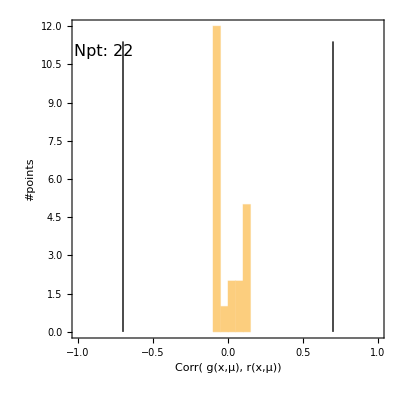
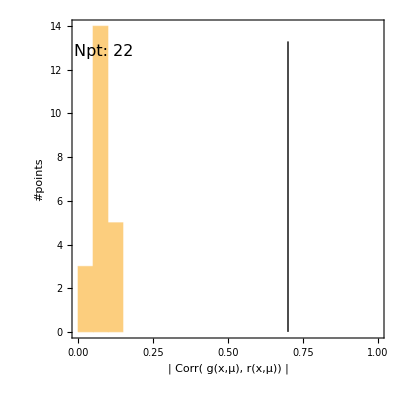
{{-Graphics-,Corr( g(x,μ), r(x,μ)) for dataset of CT14HERA2NNLO

 | 
Data Sets | 
None(225) | },{-Graphics-,-Graphics-}}

```mathematica
processdataplotsmultiexp6percentage[{corrdataclassfinal},readcorrconfigfile4[configDir,configfilename],6,0]
```

expts: {{240,241,281,266}}

can not find expt id = 240 in lisTable

can not find expt id = 241 in lisTable

can not find expt id = 281 in lisTable

can not find expt id = 266 in lisTable

making table of experiments included in plots

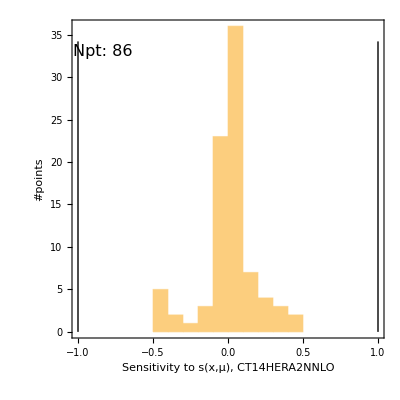
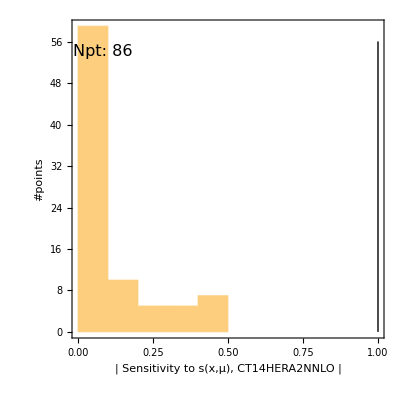
{{-Graphics-,Sensitivity to s(x,μ), CT14HERA2NNLO

 |  | 
Data Sets |  | 
None(240) | None(241) | None(281)
None(266) |  | },{-Graphics-,-Graphics-}}

```mathematica
processdataplotsmultiexp6percentage[{dRcorrdataclassfinal},readcorrconfigfile4[configDir,configfilename],5,3]
```

```mathematica
residualdataclassfinal
```

```mathematica
{{<|"label"->{"x","Q","residual"},"data"->{},"exptinfo"-><|"exptid"->225,"exptname"->"cdfLasy","feyndiagram"->"unset"|>,"PDFinfo"-><|"PDFname"->"CT14HERA2NNLO","PDFsetmethod"->"Hessian","Nset"->57,"iset"->"unset","flavour"->-5|>|>,<|"label"->{"x","Q","residual"},"data"->{},"exptinfo"-><|"exptid"->225,"exptname"->"cdfLasy","feyndiagram"->"unset"|>,"PDFinfo"-><|"PDFname"->"CT14HERA2NNLO","PDFsetmethod"->"Hessian","Nset"->57,"iset"->"unset","flavour"->-4|>|>,<|"label"->{"x","Q","residual"},"data"->{},"exptinfo"-><|"exptid"->225,"exptname"->"cdfLasy","feyndiagram"->"unset"|>,"PDFinfo"-><|"PDFname"->"CT14HERA2NNLO","PDFsetmethod"->"Hessian","Nset"->57,"iset"->"unset","flavour"->-3|>|>,<|"label"->{"x","Q","residual"},"data"->{},"exptinfo"-><|"exptid"->225,"exptname"->"cdfLasy","feyndiagram"->"unset"|>,"PDFinfo"-><|"PDFname"->"CT14HERA2NNLO","PDFsetmethod"->"Hessian","Nset"->57,"iset"->"unset","flavour"->-2|>|>,<|"label"->{"x","Q","residual"},"data"->{},"exptinfo"-><|"exptid"->225,"exptname"->"cdfLasy","feyndiagram"->"unset"|>,"PDFinfo"-><|"PDFname"->"CT14HERA2NNLO","PDFsetmethod"->"Hessian","Nset"->57,"iset"->"unset","flavour"->-1|>|>,<|"label"->{"x","Q","residual"},"data"->{},"exptinfo"-><|"exptid"->225,"exptname"->"cdfLasy","feyndiagram"->"unset"|>,"PDFinfo"-><|"PDFname"->"CT14HERA2NNLO","PDFsetmethod"->"Hessian","Nset"->57,"iset"->"unset","flavour"->0|>|>,<|"label"->{"x","Q","residual"},"data"->{},"exptinfo"-><|"exptid"->225,"exptname"->"cdfLasy","feyndiagram"->"unset"|>,"PDFinfo"-><|"PDFname"->"CT14HERA2NNLO","PDFsetmethod"->"Hessian","Nset"->57,"iset"->"unset","flavour"->1|>|>,<|"label"->{"x","Q","residual"},"data"->{LF[0.17256153384559803,80.39,1.971732954545455],LF[0.1855112310794266,80.39,1.971732954545455],LF[0.19917645454180155,80.39,1.971732954545455],LF[0.21358308834796036,80.39,1.971732954545455],LF[0.22875747653402578,80.39,1.971732954545455],LF[0.2447264230570053,80.39,1.971732954545455],LF[0.261517191794792,80.39,1.971732954545455],LF[0.16030193864596357,80.39,-0.13771569433032135],LF[0.17256153384559803,80.39,-0.13771569433032135],LF[0.1855112310794266,80.39,-0.13771569433032135],LF[0.19917645454180155,80.39,-0.13771569433032135],LF[0.21358308834796036,80.39,-0.13771569433032135],LF[0.22875747653402578,80.39,-0.13771569433032135],LF[0.2447264230570053,80.39,-0.13771569433032135],LF[0.261517191794792,80.39,-0.13771569433032135],LF[0.2791575065461639,80.39,-0.13771569433032135],LF[0.29767555103078436,80.39,-0.13771569433032135],LF[0.3170999688892017,80.39,-0.13771569433032135],LF[0.33745986368284964,80.39,-0.13771569433032135],LF[0.17256153384559803,80.39,-0.433294117647059],LF[0.1855112310794266,80.39,-0.433294117647059],LF[0.19917645454180155,80.39,-0.433294117647059],LF[0.21358308834796036,80.39,-0.433294117647059],LF[0.22875747653402578,80.39,-0.433294117647059],LF[0.2447264230570053,80.39,-0.433294117647059],LF[0.261517191794792,80.39,-0.433294117647059],LF[0.2791575065461639,80.39,-0.433294117647059],LF[0.29767555103078436,80.39,-0.433294117647059],LF[0.3170999688892017,80.39,-0.433294117647059],LF[0.33745986368284964,80.39,-0.433294117647059],LF[0.35878479889404674,80.39,-0.433294117647059],LF[0.38110479792599694,80.39,-0.433294117647059],LF[0.17256153384559803,80.39,-0.8482809123649461],LF[0.1855112310794266,80.39,-0.8482809123649461],LF[0.19917645454180155,80.39,-0.8482809123649461],LF[0.21358308834796036,80.39,-0.8482809123649461],LF[0.22875747653402578,80.39,-0.8482809123649461],LF[0.2447264230570053,80.39,-0.8482809123649461],LF[0.261517191794792,80.39,-0.8482809123649461],LF[0.2791575065461639,80.39,-0.8482809123649461],LF[0.29767555103078436,80.39,-0.8482809123649461],LF[0.3170999688892017,80.39,-0.8482809123649461],LF[0.33745986368284964,80.39,-0.8482809123649461],LF[0.35878479889404674,80.39,-0.8482809123649461],LF[0.38110479792599694,80.39,-0.8482809123649461],LF[0.4044503441027893,80.39,-0.8482809123649461],LF[0.1855112310794266,80.39,0.0921636917718761],LF[0.19917645454180155,80.39,0.0921636917718761],LF[0.21358308834796036,80.39,0.0921636917718761],LF[0.22875747653402578,80.39,0.0921636917718761],LF[0.2447264230570053,80.39,0.0921636917718761],LF[0.261517191794792,80.39,0.0921636917718761],LF[0.2791575065461639,80.39,0.0921636917718761],LF[0.29767555103078436,80.39,0.0921636917718761],LF[0.3170999688892017,80.39,0.0921636917718761],LF[0.33745986368284964,80.39,0.0921636917718761],LF[0.35878479889404674,80.39,0.0921636917718761],LF[0.38110479792599694,80.39,0.0921636917718761],LF[0.4044503441027893,80.39,0.0921636917718761],LF[0.42885238066939807,80.39,0.0921636917718761]},"exptinfo"-><|"exptid"->225,"exptname"->"cdfLasy","feyndiagram"->"unset"|>,"PDFinfo"-><|"PDFname"->"CT14HERA2NNLO","PDFsetmethod"->"Hessian","Nset"->57,"iset"->"unset","flavour"->2|>|>,<|"label"->{"x","Q","residual"},"data"->{},"exptinfo"-><|"exptid"->225,"exptname"->"cdfLasy","feyndiagram"->"unset"|>,"PDFinfo"-><|"PDFname"->"CT14HERA2NNLO","PDFsetmethod"->"Hessian","Nset"->57,"iset"->"unset","flavour"->3|>|>,<|"label"->{"x","Q","residual"},"data"->{},"exptinfo"-><|"exptid"->225,"exptname"->"cdfLasy","feyndiagram"->"unset"|>,"PDFinfo"-><|"PDFname"->"CT14HERA2NNLO","PDFsetmethod"->"Hessian","Nset"->57,"iset"->"unset","flavour"->4|>|>,<|"label"->{"x","Q","residual"},"data"->{},"exptinfo"-><|"exptid"->225,"exptname"->"cdfLasy","feyndiagram"->"unset"|>,"PDFinfo"-><|"PDFname"->"CT14HERA2NNLO","PDFsetmethod"->"Hessian","Nset"->57,"iset"->"unset","flavour"->5|>|>,<|"label"->{"x","Q","residual"},"data"->{},"exptinfo"-><|"exptid"->225,"exptname"->"cdfLasy","feyndiagram"->"unset"|>,"PDFinfo"-><|"PDFname"->"CT14HERA2NNLO","PDFsetmethod"->"Hessian","Nset"->57,"iset"->"unset","flavour"->-5|>|>,<|"label"->{"x","Q","residual"},"data"->{LF[0.19917645454180155,80.39,1.971732954545455],LF[0.21358308834796036,80.39,1.971732954545455],LF[0.22875747653402578,80.39,1.971732954545455],LF[0.2447264230570053,80.39,1.971732954545455],LF[0.261517191794792,80.39,1.971732954545455],LF[0.1855112310794266,80.39,-0.13771569433032135],LF[0.19917645454180155,80.39,-0.13771569433032135],LF[0.21358308834796036,80.39,-0.13771569433032135],LF[0.22875747653402578,80.39,-0.13771569433032135],LF[0.2447264230570053,80.39,-0.13771569433032135],LF[0.261517191794792,80.39,-0.13771569433032135],LF[0.2791575065461639,80.39,-0.13771569433032135],LF[0.29767555103078436,80.39,-0.13771569433032135],LF[0.3170999688892017,80.39,-0.13771569433032135],LF[0.33745986368284964,80.39,-0.13771569433032135],LF[0.1855112310794266,80.39,-0.433294117647059],LF[0.19917645454180155,80.39,-0.433294117647059],LF[0.21358308834796036,80.39,-0.433294117647059],LF[0.22875747653402578,80.39,-0.433294117647059],LF[0.2447264230570053,80.39,-0.433294117647059],LF[0.261517191794792,80.39,-0.433294117647059],LF[0.2791575065461639,80.39,-0.433294117647059],LF[0.29767555103078436,80.39,-0.433294117647059],LF[0.3170999688892017,80.39,-0.433294117647059],LF[0.33745986368284964,80.39,-0.433294117647059],LF[0.35878479889404674,80.39,-0.433294117647059],LF[0.38110479792599694,80.39,-0.433294117647059],LF[0.1855112310794266,80.39,-0.8482809123649461],LF[0.19917645454180155,80.39,-0.8482809123649461],LF[0.21358308834796036,80.39,-0.8482809123649461],LF[0.22875747653402578,80.39,-0.8482809123649461],LF[0.2447264230570053,80.39,-0.8482809123649461],LF[0.261517191794792,80.39,-0.8482809123649461],LF[0.2791575065461639,80.39,-0.8482809123649461],LF[0.29767555103078436,80.39,-0.8482809123649461],LF[0.3170999688892017,80.39,-0.8482809123649461],LF[0.33745986368284964,80.39,-0.8482809123649461],LF[0.35878479889404674,80.39,-0.8482809123649461],LF[0.38110479792599694,80.39,-0.8482809123649461],LF[0.4044503441027893,80.39,-0.8482809123649461],LF[0.19917645454180155,80.39,0.0921636917718761],LF[0.21358308834796036,80.39,0.0921636917718761],LF[0.22875747653402578,80.39,0.0921636917718761],LF[0.2447264230570053,80.39,0.0921636917718761],LF[0.261517191794792,80.39,0.0921636917718761],LF[0.2791575065461639,80.39,0.0921636917718761],LF[0.29767555103078436,80.39,0.0921636917718761],LF[0.3170999688892017,80.39,0.0921636917718761],LF[0.33745986368284964,80.39,0.0921636917718761],LF[0.35878479889404674,80.39,0.0921636917718761],LF[0.38110479792599694,80.39,0.0921636917718761],LF[0.4044503441027893,80.39,0.0921636917718761],LF[0.42885238066939807,80.39,0.0921636917718761]},"exptinfo"-><|"exptid"->225,"exptname"->"cdfLasy","feyndiagram"->"unset"|>,"PDFinfo"-><|"PDFname"->"CT14HERA2NNLO","PDFsetmethod"->"Hessian","Nset"->57,"iset"->"unset","flavour"->-5|>|>,<|"label"->{"x","Q","residual"},"data"->{},"exptinfo"-><|"exptid"->225,"exptname"->"cdfLasy","feyndiagram"->"unset"|>,"PDFinfo"-><|"PDFname"->"CT14HERA2NNLO","PDFsetmethod"->"Hessian","Nset"->57,"iset"->"unset","flavour"->-5|>|>}}
```

expts: {{225}}

can not find expt id = 225 in lisTable

making table of experiments included in plots

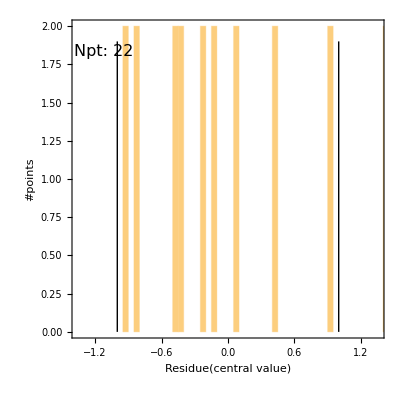
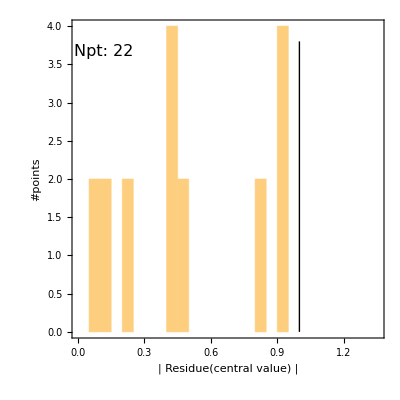
{{-Graphics-,Residue(central value) for dataset of CT14HERA2NNLO

 | 
Data Sets | 
None(225) | },{-Graphics-,-Graphics-}}

```mathematica
processdataplotsmultiexp6percentage[{residualdataclassfinal},readcorrconfigfile4[configDir,configfilename],3,1]
```

```mathematica
Show[p234[[1,1]] ]
```

-Graphics-

expts: {{225}}

can not find expt id = 225 in lisTable

making table of experiments included in plots

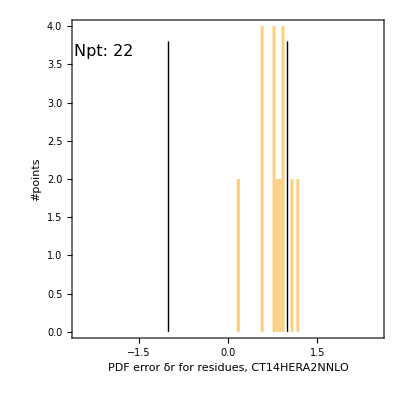
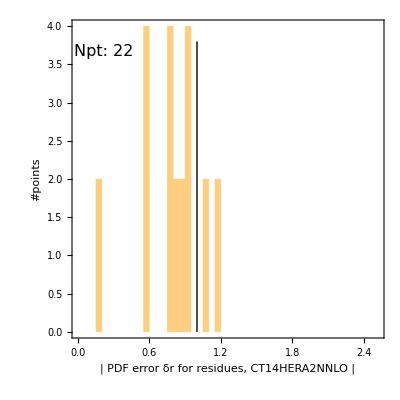
{{-Graphics-,PDF error δr for residues, CT14HERA2NNLO

 | 
Data Sets | 
None(225) | },{-Graphics-,-Graphics-}}

```mathematica
processdataplotsmultiexp6percentage[{dRdataclassfinal},readcorrconfigfile4[configDir,configfilename],4,1]
```

expts: {{240,241,281,266}}

can not find expt id = 240 in lisTable

can not find expt id = 241 in lisTable

can not find expt id = 281 in lisTable

can not find expt id = 266 in lisTable

making table of experiments included in plots

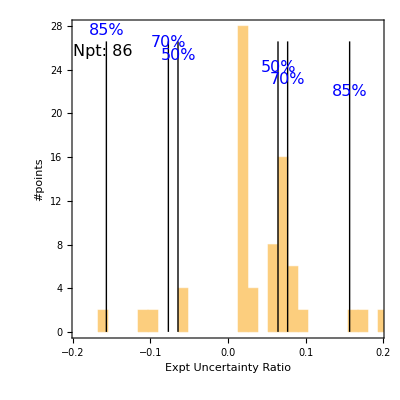
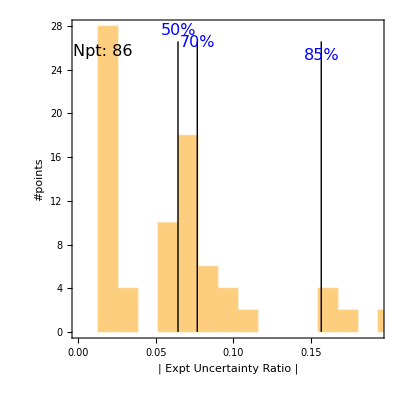
{{-Graphics-,Expt Uncertainty Ratio for dataset of CT14HERA2NNLO

 |  | 
Data Sets |  | 
None(240) | None(241) | None(281)
None(266) |  | },{-Graphics-,-Graphics-}}

```mathematica
processdataplotsmultiexp6percentage[{expterrordataclassfinal},readcorrconfigfile4[configDir,configfilename],2,0]
```

```mathematica
Export["testreso.eps",processdataplotsmultiexp6percentage[{expterrordataclassfinal},readcorrconfigfile4[configDir,configfilename],2,0][[1,1]],ImageResolution->imgresol]
```

expts: {{240,241,281,266}}

can not find expt id = 240 in lisTable

can not find expt id = 241 in lisTable

can not find expt id = 281 in lisTable

can not find expt id = 266 in lisTable

making table of experiments included in plots

testreso.eps

```mathematica
imgresol=144
```

144

```mathematica
NotebookDirectory[]
```

/home/botingw/code/pdf_correlation/code/math_corr_datasets/mathscript_v21_copy1/bin/

```mathematica
Directory[]
```

/home/botingw/code/pdf_correlation/code/math_corr_datasets/mathscript_v21_copy1/bin

```mathematica
readcorrconfigfile4[configDir,configfilename]
```

{457,2017.0518.0238.-0500_ct14nn-new,{1,2,3,4,5,6,7},{1,1,1,1,1,1,0},{701,702,703,159,101,102,103,104,106,108,109,110,111,124,125,126,127,147,201,203,204,225,227,231,234,260,261,504,514,145,169,267,268,535,240,241,281,265,266,538,245,246,247,542,544,249,250,565,566,567,568},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0},{bb,cb,sb,db,ub,g,u,d,s,c,b,q6,q7,q8,user},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,0}, sigma_Higgs (pb),{0.012,0.012,0.012,0.014,0.012,0.012,0.012,0.032,0.012,0.012,0.012,0.015,0.012,0.012,0.052,0.012,0.012,0.022,0.012,0.0432,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.022,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012},{0.00001,1},{10.,2000.},auto,{auto,auto},{0,auto},{50,70,85},tiny,{1,2,3,4,5,6,7},{0,2,1,1,1,1,1},{0.5,0.75,0.,0.15,0.7,100.,0.7,100.,0.7,100.,0.7,1.,0.45,0.75},{50,86.55,85,100,85,100,85,100,50,85,50,85,50,85}}

```mathematica
readcorrconfigfile4[NotebookDirectory[],configfilename]
```

{457,2017.0518.0238.-0500_ct14nn-new,{1,2,3,4,5,6,7},{1,1,1,1,1,1,0},{701,702,703,159,101,102,103,104,106,108,109,110,111,124,125,126,127,147,201,203,204,225,227,231,234,260,261,504,514,145,169,267,268,535,240,241,281,265,266,538,245,246,247,542,544,249,250,565,566,567,568},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0},{bb,cb,sb,db,ub,g,u,d,s,c,b,q6,q7,q8,user},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,0}, sigma_Higgs (pb),{0.012,0.012,0.012,0.014,0.012,0.012,0.012,0.032,0.012,0.012,0.012,0.015,0.012,0.012,0.052,0.012,0.012,0.022,0.012,0.0432,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.022,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012},{0.00001,1},{10.,2000.},auto,{auto,auto},{0,auto},{50,70,85},tiny,{1,2,3,4,5,6,7},{0,2,1,1,1,1,1},{0.5,0.75,0.,0.15,0.7,100.,0.7,100.,0.7,100.,0.7,1.,0.45,0.75},{50,86.55,85,100,85,100,85,100,50,85,50,85,50,85}}

```mathematica
readcorrconfigfile4[Directory[]<>"/",configfilename]
```

{457,2017.0518.0238.-0500_ct14nn-new,{1,2,3,4,5,6,7},{1,1,1,1,1,1,0},{701,702,703,159,101,102,103,104,106,108,109,110,111,124,125,126,127,147,201,203,204,225,227,231,234,260,261,504,514,145,169,267,268,535,240,241,281,265,266,538,245,246,247,542,544,249,250,565,566,567,568},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0},{bb,cb,sb,db,ub,g,u,d,s,c,b,q6,q7,q8,user},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,0}, sigma_Higgs (pb),{0.012,0.012,0.012,0.014,0.012,0.012,0.012,0.032,0.012,0.012,0.012,0.015,0.012,0.012,0.052,0.012,0.012,0.022,0.012,0.0432,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.022,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012},{0.00001,1},{10.,2000.},auto,{auto,auto},{0,auto},{50,70,85},tiny,{1,2,3,4,5,6,7},{0,2,1,1,1,1,1},{0.5,0.75,0.,0.15,0.7,100.,0.7,100.,0.7,100.,0.7,1.,0.45,0.75},{50,86.55,85,100,85,100,85,100,50,85,50,85,50,85}}

```mathematica
FileNames[Directory[]]
FileNames[Directory[]<>"/"]
```

{/home/botingw/code/pdf_correlation/code/math_corr_datasets/mathscript_v21_copy1/bin}

{/home/botingw/code/pdf_correlation/code/math_corr_datasets/mathscript_v21_copy1/bin}

```mathematica
testnewindex=Import[CorrDataDir<>"expterror_"<>CorrDataFile,"ExpressionML"];
```

```mathematica
testnewindex[[1]]
```

<|label→{x,Q,expterror/exptcentral},data→{LF[0.101,2.328,0.123077],LF[0.167,2.994,0.113874],LF[0.326,4.182,0.123858],LF[0.057,2.295,0.100007],LF[0.101,3.055,0.0999652],LF[0.167,3.928,0.100094],LF[0.326,5.489,0.110615],LF[0.057,2.698,0.0965188],LF[0.101,3.592,0.106374],LF[0.167,4.618,0.118621],LF[0.326,6.452,0.130294],LF[0.057,2.457,0.104641],LF[0.101,3.271,0.0958001],LF[0.167,4.206,0.0989567],LF[0.326,5.877,0.107182],LF[0.057,3.225,0.098301],LF[0.101,4.293,0.100947],LF[0.167,5.52,0.102872],LF[0.326,7.712,0.118939],LF[0.021,2.301,0.0952787],LF[0.057,3.791,0.0903334],LF[0.101,5.046,0.100485],LF[0.167,6.488,0.11441],LF[0.326,9.065,0.132874],LF[0.057,2.925,0.108059],LF[0.101,3.894,0.102769],LF[0.167,5.007,0.102525],LF[0.326,6.996,0.115866],LF[0.021,2.33,0.117615],LF[0.057,3.839,0.115806],LF[0.101,5.11,0.112213],LF[0.167,6.571,0.116658],LF[0.326,9.181,0.131031],LF[0.021,2.739,0.119099],LF[0.057,4.512,0.103225],LF[0.101,6.007,0.102362],LF[0.167,7.724,0.130126],LF[0.326,10.79,0.161126]},exptinfo→<|exptid→124,exptname→NuTvNuChXN,feyndiagram→unset|>,PDFinfo→<|PDFname→CT14HERA2NNLO,PDFsetmethod→Hessian,Nset→unset,iset→unset,flavour→unset|>,rawdata→{124,NuTvNuChXN,     Q          x         y          Exp      Th./Norm     TotErr     EXP/FIT  ERR/FIT    ChiSq  Shift    ShiftedData  UnCorErr  ReducedChi2  lob/lio,1.,38,R^2, r(k) =    0.000  -0.017,-2.27713,R^2, r(k) =    0.000  -0.017}|>

```mathematica
CorrDataDir
```

../quick_data/

```mathematica
Get["corr_proj_funcs.m"]
```

present directory: /home/botingw/Downloads/Sean_20171114/xqplotter-master/bin

loading ../lib/pdfParsePDS2013.m

loading ../lib/dtareadbotingw2016.m

expts: {{159}}

can not find expt id = 159 in lisTable

making table of experiments included in plots

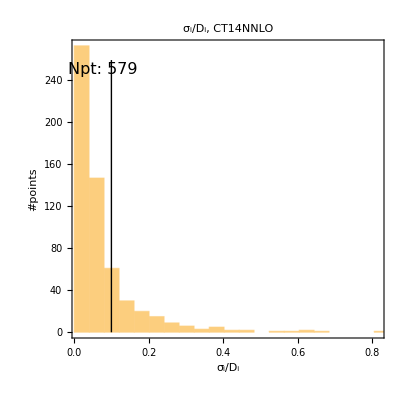
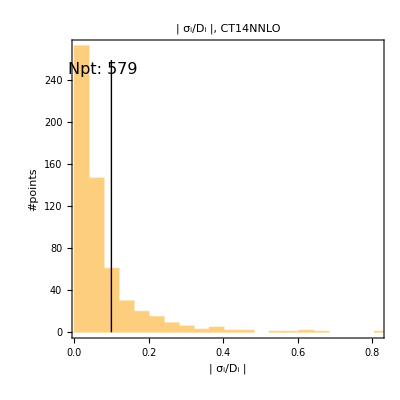
{{-Graphics-,σ_i/D_i, CT14NNLO

 | 
Data Sets | 
None(159) | },{-Graphics-,-Graphics-}}

```mathematica
processdataplotsmultiexp7percentage[{expterrordataclassfinal},readcorrconfigfile5[configDir,configfilename],2,flavour]
```

expts: {{159}}

can not find expt id = 159 in lisTable

making table of experiments included in plots

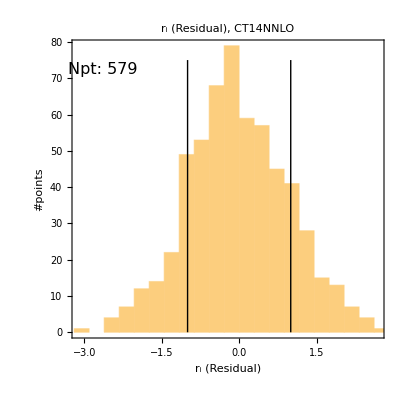
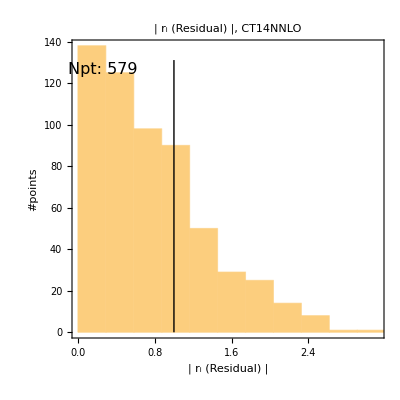
{{-Graphics-,r_i (Residual), CT14NNLO

 | 
Data Sets | 
None(159) | },{-Graphics-,-Graphics-}}

```mathematica
processdataplotsmultiexp7percentage[{residualdataclassfinal},readcorrconfigfile5[configDir,configfilename],3,flavour]
```

expts: {{159}}

can not find expt id = 159 in lisTable

making table of experiments included in plots

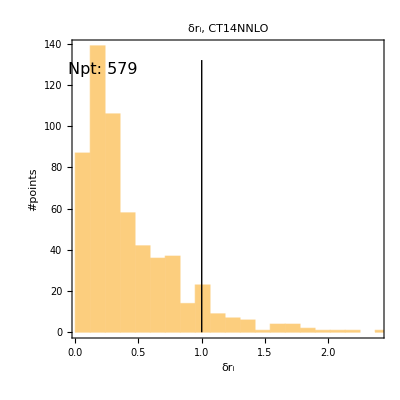
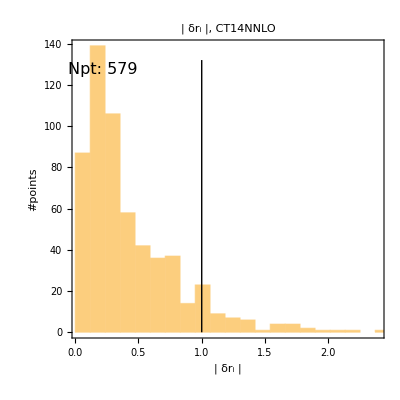
{{-Graphics-,δr_i, CT14NNLO

 | 
Data Sets | 
None(159) | },{-Graphics-,-Graphics-}}

```mathematica
processdataplotsmultiexp7percentage[{dRdataclassfinal},readcorrconfigfile5[configDir,configfilename],4,flavour]
```

expts: {{160}}

can not find expt id = 160 in lisTable

making table of experiments included in plots

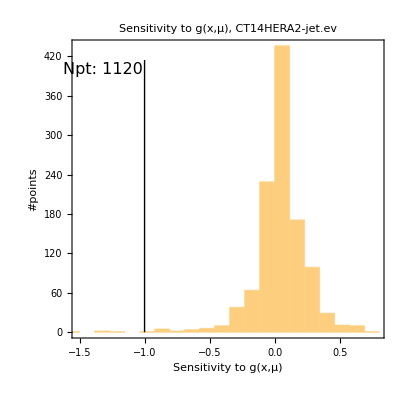
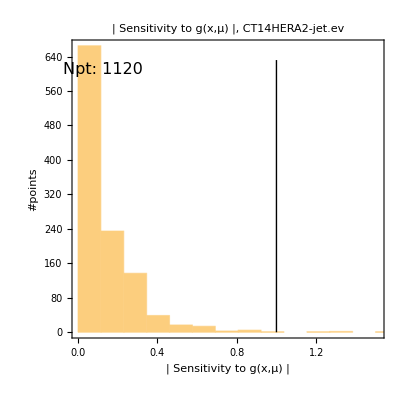
{{-Graphics-,Sensitivity to g(x,μ), CT14HERA2-jet.ev

 | 
Data Sets | 
None(160) | },{-Graphics-,-Graphics-}}

```mathematica
processdataplotsmultiexp7percentage[{dRcorrdataclassfinal},readcorrconfigfile5[configDir,configfilename],5,0]
```

expts: {{160}}

can not find expt id = 160 in lisTable

making table of experiments included in plots

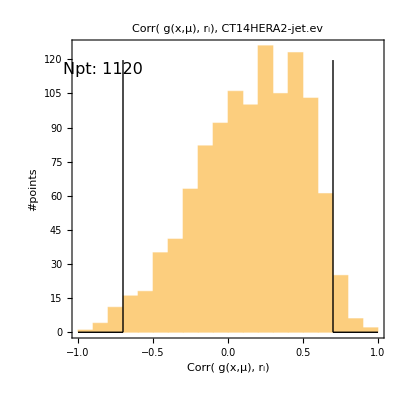
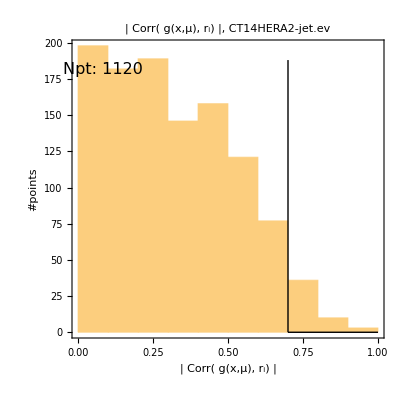
{{-Graphics-,Corr( g(x,μ), r_i), CT14HERA2-jet.ev

 | 
Data Sets | 
None(160) | },{-Graphics-,-Graphics-}}

```mathematica
processdataplotsmultiexp7percentage[{corrdataclassfinal},readcorrconfigfile5[configDir,configfilename],6,0 ]
```

```mathematica
Get["corr_proj_funcs.m"]
```

present directory: /home/botingw/Downloads/Sean_20171114/xqplotter-2447ceacd1447536c690310f5ca37f4e39baa187/bin

loading ../lib/pdfParsePDS2013.m

loading ../lib/dtareadbotingw2016.m

```mathematica
ReadUserFunction[Directory[]<>"/","user_define_func.txt"]
```

{ sigma_Higgs (pb),{0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012}}

```mathematica
(*{Jobid,PDFname,FigureType,FigureFlag,ExptidType,ExptidFlag,CorrelationArgType,CorrelationArgFlag,UserArgName,UserArgValue,
XQfigureXrange,XQfigureYrange,Hist1figureNbin,Hist1figureXrange,(*Hist1figureYrange*)dummy12,
ColorSeperator,
Size,HighlightType,HighlightMode,HighlightMode1,HighlightMode2}=*)
readcorrconfigfile4[configDir,configfilename]
readcorrconfigfile5[configDir,configfilename][[-2]]
```

{70805,CT14NNLO,{1,2,3,4,5,6,7},{1,1,1,1,1,1,0},{701,702,703,159,101,102,103,104,106,108,109,110,111,124,125,126,127,147,201,203,204,225,227,231,234,260,261,504,514,145,169,267,268,535,240,241,281,265,266,538},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0},{bb,cb,sb,db,ub,g,u,d,s,c,b,q6,q7,q8,user},{0,0,0,0,0,1,0,0,0,0,0,0,0,0,0}, ,{},{0.00001,1.},{1.,2000.},auto,{auto,auto},{0,auto},{50,70,85},tiny,{1,2,3,4,5,6,7},{0,2,2,2,2,2,1},{1.,5.,0.2,10,1.,5.,1.,5.,1.,5.,0.7,1.,1.,5.},{0.,0.,85,100,85,100,85,100,85,100,85,100,0.,0.}}

Read::readn: Invalid real number found when reading from StringToStream[unset].

Part::partw: Part 2 of {$Failed} does not exist.

Read::readn: Invalid real number found when reading from StringToStream[unset].

Part::partw: Part 2 of {$Failed} does not exist.

Read::readn: Invalid real number found when reading from StringToStream[unset].

General::stop: Further output of Read::readn will be suppressed during this calculation.

Part::partw: Part 2 of {$Failed} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

ReadList::readn: Invalid real number found when reading from StringToStream[unset].

{unset}

```mathematica
(*20171109: seperate user difine function/data IO and configure file*)
userfuncfilename="user_define_func.txt";
{UserArgName,UserArgValue}=ReadUserFunction["./",userfuncfilename]
```

{ sigma_Higgs (pb),{0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012,0.012}}

```mathematica
ReadUserFunctionV3["./",userfuncfilename]
```

```mathematica
fxQsamept2classfinal[[3,17]]
```

Part::partw: Part 3 of {{«1»},{«1»}} does not exist.

1⟦3,17⟧
 |  |  |  |

```mathematica
exptidDir
```

StringDrop[,-1]<>/

```mathematica
exptid
```

101

```mathematica
fxQDatabaseExptlist
```

{101,102,104,106,108,109,110,111,124,125,126,127,145,147,159,169,201,203,204,225,227,234,240,241,260,261,266,267,268,281,504,514,535,538}

```mathematica
((fxQDatabaselist[[1,iu+6,3]]/.LF->List)-(fxQDatabaselist[[1,iubar+6,3]]/.LF->List))/((fxQDatabaselist[[1,iu+6,3]]/.LF->List)+(fxQDatabaselist[[1,iubar+6,3]]/.LF->List))
fxQsamept2classfinal[[2,-1]][["data"]][[1]]
```

{0.,0.,0.73252,0.739896,0.737092,0.737801,0.732453,0.733104,0.733845,0.740846,0.727685,0.726688,0.737235,0.729246,0.739421,0.730101,0.733949,0.731093,0.738179,0.71995,0.746273,0.730365,0.735003,0.732212,0.732774,0.723387,0.742542,0.736026,0.729819,0.735491,0.727436,0.737356,0.729457,0.725302,0.743687,0.730909,0.733941,0.73306,0.732583,0.728924,0.736762,0.727223,0.740451,0.731621,0.732744,0.730706,0.733423,0.743015,0.727697,0.715237,0.748441,0.738931,0.724507,0.733199,0.729687,0.732723,0.735427,0.728392,0.72429}

LF[0.0457788,80.38,0.73252,0.739896,0.737092,0.737801,0.732453,0.733104,0.733845,0.740846,0.727685,0.726688,0.737235,0.729246,0.739421,0.730101,0.733949,0.731093,0.738179,0.71995,0.746273,0.730365,0.735003,0.732212,0.732774,0.723387,0.742542,0.736026,0.729819,0.735491,0.727436,0.737356,0.729457,0.725302,0.743687,0.730909,0.733941,0.73306,0.732583,0.728924,0.736762,0.727223,0.740451,0.731621,0.732744,0.730706,0.733423,0.743015,0.727697,0.715237,0.748441,0.738931,0.724507,0.733199,0.729687,0.732723,0.735427,0.728392,0.72429]

```mathematica
((fxQDatabaselist[[10,iu+6,1]]/.LF->List)-(fxQDatabaselist[[10,iubar+6,1]]/.LF->List))/((fxQDatabaselist[[10,iu+6,1]]/.LF->List)+(fxQDatabaselist[[10,iubar+6,1]]/.LF->List))
fxQsamept2classfinal[[1,-2]][["data"]][[1]]
fxQsamept2classfinal[[1,1]][["exptinfo","exptid"]]
```

{0.,0.,0.767313,0.774295,0.771563,0.770956,0.767449,0.768422,0.767628,0.774979,0.763023,0.762259,0.77139,0.764176,0.773848,0.764799,0.769074,0.765233,0.774406,0.755397,0.780305,0.765556,0.7694,0.767543,0.767253,0.758681,0.776735,0.772911,0.762984,0.769194,0.76411,0.772426,0.76408,0.760625,0.777586,0.765114,0.769266,0.767729,0.767396,0.76444,0.77077,0.762994,0.774419,0.765861,0.768338,0.766176,0.767648,0.776773,0.762919,0.750987,0.782312,0.773,0.75975,0.767026,0.765635,0.766226,0.768834,0.764391,0.757922}

LF[0.114,2.411,0.767313,0.774295,0.771563,0.770956,0.767449,0.768422,0.767628,0.774979,0.763023,0.762259,0.77139,0.764176,0.773848,0.764799,0.769074,0.765233,0.774406,0.755397,0.780305,0.765556,0.7694,0.767543,0.767253,0.758681,0.776735,0.772911,0.762984,0.769194,0.76411,0.772426,0.76408,0.760625,0.777586,0.765114,0.769266,0.767729,0.767396,0.76444,0.77077,0.762994,0.774419,0.765861,0.768338,0.766176,0.767648,0.776773,0.762919,0.750987,0.782312,0.773,0.75975,0.767026,0.765635,0.766226,0.768834,0.764391,0.757922]

125